# MathIOmica: Omics Analysis Tutorial

Loading the MathIOmica Packagepaclet:MathIOmica/tutorial/MathIOmicaTutorial#2133290847 | Metabolomic Datapaclet:MathIOmica/tutorial/MathIOmicaTutorial#779816621
Data in MathIOmicapaclet:MathIOmica/tutorial/MathIOmicaTutorial#671613477 | Combined Data Clusteringpaclet:MathIOmica/tutorial/MathIOmicaTutorial#1340833355
Transcriptome Datapaclet:MathIOmica/tutorial/MathIOmicaTutorial#540567276 | Visualizationpaclet:MathIOmica/tutorial/MathIOmicaTutorial#1200455778
Proteomic Datapaclet:MathIOmica/tutorial/MathIOmicaTutorial#1387790784 | Annotation and Enrichmentpaclet:MathIOmica/tutorial/MathIOmicaTutorial#2035743524

MathIOmica is an omics analysis package designed to facilitate method development for the analysis of multiple omics in Mathematica, particularly for dynamics (time series/longitudinal data). This extensive tutorial follows the analysis of multiple dynamic omics data (transcriptomics, proteomics, and metabolomics from human samples). Various MathIOmica functions are introduced in the tutorial, including additional discussion of related functionality. We should note that the approach methods are simply an illustration of MathIOmica functionality, and should not be considered as a definitive approach. Additionally, certain details are included to illustrate common complications (e.g. renaming samples, combining datasets, transforming accessions from one database to another, dealing with replicates and Missing data, etc.).

After a brief discussion of data in MathIOmica, each example data (transcriptome, proteome and metabolome) are imported and preprocessed. Next a simulation is carried out to obtain datasets for each omics used to assess statistical significance cutoffs. The datasets are combined, and classified for time series patterns, followed by clustering. The clusters are visualized, and biological annotation of Gene Ontology (GO) and pathway analysis (KEGG: Kyoto Encyclopedia of Genes and Genomes) are finally considered.

N.B.1 For a more streamlined/simple example with less discussion please check out the tutorial on MathIOmica Dynamic Transcriptome.

N.B.2 We highly recommend the saving of intermediate results whenever possible. Some functions perform lengthy intensive computations and the performance may vary from system to system. Please use Putpaclet:ref/Put to save expressions to a file, and equivalently Getpaclet:ref/Get to recover these expressions.

## Loading the MathIOmica Package

The functions defined in the MathIOmica` context provide support for conducting analyses of omics data (See also the MathIOmica Overview).

This loads the package:

```mathematica
<<MathIOmica`
```

Also we can load MathIOmica as:

```mathematica
Needs["MathIOmica`"]
```

## Data in MathIOmica

In this section we will discuss the data objects in use by MathIOmica, particularly the format of an OmicsObject. The data in the tutorial will be imported as an OmicsObject which is first described in this section. Then we present the example data included with MathIOmica. The example data will be imported in subsequent sections to illustrate analysis methods available in MathIOmica.

### Data Format: OmicsObject

In MathIOmica the calculations utilize what we term an omics object (OmicsObject). An OmicsObject is an association of associations with some additional characteristics. It has an external  (outer) association to denote samples and an internal (inner) association for annotation.

#### OmicsObject Structure

In an OmicsObject the outer association has M outer labels as keys, corresponding to M samples. Across the samples there are N inner labels (e.g. identifiers for genes/proteins), and  inner labels are the same across samples. For a given j^th outer label, OuterLabel_j, the k^th inner label, InnerLabel_k has a value of :

InnerLabel_k→ {{Measurements_jk},{Metadata_jk}}

OmicsObject structure:

<|OuterLabel_1→ <|InnerLabel_1→ {{Measurements_11},{Metadata_11}},
InnerLabel_2→ {{Measurements_12},{Metadata_12}},
InnerLabel_3→ {{Measurements_13},{Metadata_13}},
...,
InnerLabel_k→ {{Measurements_(1k)},{Metadata_(1k)}},
...,
InnerLabel_N→ {{Measurements_(1N)},{Metadata_(1N)}}|>,
OuterLabel_2→ <|InnerLabel_1→ {{Measurements_21},{Metadata_21}},
InnerLabel_2→ {{Measurements_22},{Metadata_22}},
InnerLabel_3→ {{Measurements_23},{Metadata_23}},
...,
InnerLabel_k→ {{Measurements_(2k)},{Metadata_(2k)}},
...,
InnerLabel_N→ {{Measurements_(2N)},{Metadata_(2N)}}|>,
...,
OuterLabel_j→ <|InnerLabel_1→ {{Measurements_j1},{Metadata_j1}},
InnerLabel_2→ {{Measurements_j2},{Metadata_j2}},
InnerLabel_3→ {{Measurements_j3},{Metadata_j3}},
...,
InnerLabel_k→ {{Measurements_jk},{Metadata_jk}},
...,
InnerLabel_N→ {{Measurements_jN},{Metadata_jN}}|>,
...,
OuterLabel_M→ <|InnerLabel_1→ {{Measurements_M1},{Metadata_M1}},
InnerLabel_2→ {{Measurements_M2},{Metadata_M2}},
InnerLabel_3→ {{Measurements_M3},{Metadata_M3}},
...,
InnerLabel_k→ {{Measurements_Mk},{Metadata_Mk}},
...,
InnerLabel_N→ {{Measurements_MN},{Metadata_MN}}|>
|>

For any j^th outer label, OuterLabel_j, it is possible that the m^th inner label, InnerLabel_m is missing and takes a Missing[] value in the form InnerLabel_m→ Missing[]. This can happen if the measurement was not performed for the sample, or no value was recorded (e.g. mass spectrometry data).

For example here is a list of 3 samples using protein identifiers (specifically, these are UniProt accessions). The measurements are relative intensities in this case and the metadata is the number of peptides per sample.

```mathematica
omicsObjectExample=<|"FirstSample"-><|{"A0AVT1"}->{{0.937},{17}},{"A0MZ66"}->{{1.059},{9}},{"A1A4S6"}->{{1.03},{11}},{"A1L0T0"}->{{1.268},{4}},{"A0FGR8"}->Missing[]|>,"SecondSample"-><|{"A0AVT1"}->{{1.003},{17}},{"A0MZ66"}->Missing[],{"A1A4S6"}->{{0.779},{11}},{"A1L0T0"}->{{0.917},{4}},{"A0FGR8"}->{{0.921},{24}}|>,"ThirdSample"-><|{"A0AVT1"}->{{1.064},{19}},{"A0MZ66"}->Missing[],{"A1A4S6"}->{{0.545},{5}},{"A1L0T0"}->Missing[],{"A0FGR8"}->{{0.87},{23}}|>|>;
```

The outer labels of an OmicsObject are strings, while the inner labels are typically lists of strings.

#### Methods to Import Data as an OmicsObject

There are multiple methods to import data as an OmicsObject using MathIOmica. Four functions assist with importing data directly from text files:

(i) DataImporterpaclet:MathIOmica/ref/DataImporter provides a graphical dynamic interface that utilizes file headers to assist with the creation of OmicsObject variables from multiple files.

(ii) The OmicsObjectCreatorpaclet:MathIOmica/ref/OmicsObjectCreator function provides a function to create an OmicsObject from already existing/imported data in a Mathematica notebook.

(iii) DataImporterDirectpaclet:MathIOmica/ref/DataImporterDirect and (iv) DataImporterDirectLabeledpaclet:MathIOmica/ref/DataImporterDirectLabeled provide additional expert mode functions that may be used to directly import data as OmicsObject variables without a graphical interface.

DataImporter[associationName]  | provides a graphical interface to extract data and create an OmicsObject variable associationName for associations of information.
OmicsObjectCreator[outerLabels, innerLabels, measurements,metadata] | creates an OmicsObjectpaclet:MathIOmica/ref/OmicsObject for use with MathIOmica. It uses the following inputs:
       | outerLabels | Outer labels (keys) for the OmicsObject.
       | innerLabels | Inner labels (keys) for identifiers in the OmicsObject.
       | measurements | List of measurements for each inner label.
       | metadata | List of metadata for each label.
DataImporterDirect[positionsList, fileList, headerLines] | Expert Usage: The DataImporterDirectpaclet:MathIOmica/ref/DataImporterDirect function is a helper function originally created for DataImporterpaclet:MathIOmica/ref/DataImporter. DataImporterDirectpaclet:MathIOmica/ref/DataImporterDirect[positionsList, fileList, headerLines] creates an OmicsObject importing the column number in positionsList  from the fileList file path list, and importing data by skipping a number of headerLines.
DataImporterDirectLabeled[sampleRules, fileList, headerLines, headerColumnAssociations] | Expert Usage: The DataImporterDirectLabeledpaclet:MathIOmica/ref/DataImporterDirectLabeled function creates an OmicsObject association for variableName, by imporing data from the files at the paths specified in the fileList, using the sampleRules as a label to column header imported rule for each file, and the headerColumnAssociations list of associations to associate column headers to column positions for each file.

Functions for importing/creating OmicsObject datasets.

#### Working with OmicsObject Data

An OmicsObject is an association of associations, and so Query can be used directly to access and manipulate components. MathIOmica also offers multiple functions that can implement computations and manipulation of an OmicsObject:

Applier[function, inputData] | applies function to OmicsObject, association or list inputData components.
ApplierList[function, inputData] | applies function to list of lists from an association, nested association or components or a matrix inputData.
ConstantAssociator[inputAssociation, associationAddition] | adds multi key constant to an OmicsObject (or an association of associations) inputAssociation, with each addition specified in a single association associationAddition, of form <|addition1→ Value1,addition2→ Value2,...|>.
CreateTimeSeries[dataIn] | creates a time series list across an OmicsObject dataIn using outer Keys for points.
EnlargeInnerAssociation[omicsObjectList] | combines a list of OmicsObject (associations of associations)  omicsObjectList elements  by enlarging the inner associations - inner association Keys must be different.
EnlargeOuterAssociation[omicsObjectList] | combines a list, omicsObjectList, of OmicsObject (or associations of associations) elements to a combined output by enlarging the outer associations - outer association keys must be different.
FilteringFunction[omicsObject,cutoff] | filters an OmicsObject data by a chosen comparison (by default greatr or equal) to a cutoff.
FilterMissing[omicsObject, percentage] | filters out data from omicsObject if across the datasets a percentage of data points is missing.
LowValueTag[omicsObject, valueCutoff] | takes an omicsObject and tags values in specified position as Missingpaclet:ref/Missing[] based on provided valueCutoff.
MeasurementApplier[function,omicsObject] | applies a function to the measurement list of an omicsObject, ignoring missing values.
OmicsObjectMerge[{omicsObject_1,omicsObject_2, …},f] | merges a list of OmicsObject components {omicsObject_1,omicsObject_2, …}, using the function f to combine values with the same inner and outer keys.
OmicsObjectPairedMerge[omicsObject_1,omicsObject_2] | merges pairwise omicsObject1 and omicsObject2 values that have the same inner and outer keys.
Returner[originalAssociation, update] | returns a modified originalAssociation updated at a specified position by the single association update, e.g. from Applierpaclet:MathIOmica/ref/Applier or ApplierListpaclet:MathIOmica/ref/ApplierList result.

Functions for manipulating OmicsObject datasets.

### Example Data

MathIOmica comes with multiple example data. The data can be found in the ConstantMathIOmicaExamplesDirectorypaclet:MathIOmica/ref/ConstantMathIOmicaExamplesDirectory:

We can get a listing of the current example Data by evaluating:

```mathematica
FileNames[__,ConstantMathIOmicaExamplesDirectory]
```

The data contains both initial (raw) data and additionally intermediate data that have been analyzed in MathIOmica and are used in the examples (N.B. these files should not be altered or removed). The dynamic raw datasets are from an integrative Personal Omics Profile as described below:

integrative Personal Omics Profiling (iPOP)
 | Data from the first integrative Omics Profiling (iPOP) is used comprised of dynamics from proteomics transcriptomics and metabolomics. The data corresponds to a time series analysis of omics from blood componenets from a single individual.
Different samples (from 7 to 21 included here) were obtained at different time points. The time points included here correspond to days ranging from 186th to the 400th day of the study, (this can be represented in the following sample to day association: <|7→186,8→255,9→289,10→290,11→292,12→294,13→297,14→301,15→307,16→311,17→322,18→329,19→369,20→380,21→400|>. On day 289 the subject of the study had a Respiratory syncytial virus infection. Additionally, after day 301, the subject displayed high glucose levels and was eventually diagnosed with type 2 diabetes. The analyzed mapped data are used in these examples for illustrative purposes - these and additional dynamic omics data that will become available can also be accessed MathIOmica website at https://mathiomica.org. More information regarding the iPOP dataset can also be found in the original iPOP paper: Chen^*,Mias^*,Li-Pook-Than^*,Jiang^* et al.,Personal Omics Profiling Reveals Dynamic Molecular and Medical Phenotypes.  Cell 148(6),p1293 (2012),PMID:22424236.
http://dx.doi.org/10.1016/j.cell.2012.02.009.
and related review (including summary):
Mias and Snyder Personal Genomes Quantitative Dynamic Omics and Personalized Medicine.  
Quantitative Biology 1(1) (2013), PMCID:PMC4366006.
http://dx.doi.org/10.1007/s40484-013-0005-3.
Example iPOP Set Description | File Names located in the ConstantMathIOmicaExamplesDirectory.
iPOP Transcriptome. The transcriptomic data included was obtained from mapping of the  originally RNA Sequencing raw data using the Tuxedo suite. The data corresponds to transcriptome from peripheral blood mononuclear cells (PBMCs). | iPOP_ 07_genes.fpkm_tracking
iPOP_ 08_genes.fpkm_tracking
iPOP_ 09_genes.fpkm_tracking
iPOP_ 10_genes.fpkm_tracking
iPOP_ 11_genes.fpkm_tracking
iPOP_ 12_genes.fpkm_tracking
iPOP_ 13_genes.fpkm_tracking
iPOP_ 14_genes.fpkm_tracking
iPOP_ 15_genes.fpkm_tracking
iPOP_ 16_genes.fpkm_tracking
iPOP_ 17_genes.fpkm_tracking
iPOP_ 18_genes.fpkm_tracking
iPOP_ 19_genes.fpkm_tracking
iPOP_ 20_genes.fpkm_tracking
iPOP_ 21_genes.fpkm_tracking
iPOP Proteome. The Proteomics data from analysis of mass spectrometry data using the Sequest algorithm implemented by ProteomeDiscoverer. The data corresponds to proteome from PBMCs.
The names of the files provide a correspondence of samples to Tandem Mass Tag labels in order of increasing m/z values  from 126 to 131 amu. 6 TMT labels were used in each experiment.
The data has been adapted from the original to UniProt accessions. | 8_7_9_10_11_14_MulticonsensusReports_3Replicates.csv
8_12_13_15_16_14_MulticonsensusReports_3Replicates.csv
8_17_19_20_21_14_MulticonsensusReports_3Replicates.csv
iPOP Metabolome. The Metabolomics data from analysis of mass spectrometry data. The data corresponds to small molecule metabolomics from plasma ran with technical triplicates.
The names of the files provide a correspondence of samples ran in positive or negative mode. | metabolomics_negative_mode.csv
metabolomics_positive_mode.csv

Description of Example iPOP original datasets and corresponding files in the ConstantMathIOmicaExamplesDirectorypaclet:MathIOmica/ref/ConstantMathIOmicaExamplesDirectory. N.B. this table is provided as a reference for the examples, and these files should not be altered or removed.

Various analyzed datasets are used in the MathIOmica documentation for examples:

Data  Description | File Name(s) located in the  ConstantMathIOmicaExamplesDirectory.
iPOP transcriptome imported as an OmicsObject across all timepoints. | rnaExample
iPOP proteome data imported as an OmicsObject across all timepoints. | proteinExample
iPOP metabolome data imported as an OmicsObject across all timepoints and technical replicates for negative and positive mode aligned mass spectrometry features. | metabolomicsNegativeModeExample
metabolomicsPositiveModeExample
Example time series from proteomics. | proteinTimeSeriesExample
Example classification results from proteomics. | proteinClassificationExample
Example classification results from proteomics. | proteinClusteringExample
Example combined clustering results from transcriptome, proteome and metabolome data. | combinedClustersExample
Example enrichment analysis results for Gene Ontology and KEGG pathway analysis for combined omics data in this tutorial. | combinedGOAnalysis
combinedKEGGAnalysis
Spectra from proteomics mass spectrometry data examples. | small.pwiz.1.1.mzML
exampleMS3.mzXML

Description of example analyzed datasets and corresponding files in the ConstantMathIOmicaExamplesDirectorypaclet:MathIOmica/ref/ConstantMathIOmicaExamplesDirectory. N.B. this table is provided as a reference for the examples, and these files should not be altered or removed.

## Transcriptome Data

In this section we import the example transcriptome iPOP dataset, and illustrate a preprocessing approach for this omic dataset.

### Importing OmicsObject Transcriptome Data

We first import the transcriptomics data example (for details on how to import such data please refer to DataImporterpaclet:MathIOmica/ref/DataImporter, DataImporterDirectpaclet:MathIOmica/ref/DataImporterDirect, DataImporterDirectLabeledpaclet:MathIOmica/ref/DataImporterDirectLabeled and OmicsObjectCreatorpaclet:MathIOmica/ref/OmicsObjectCreator documentation).

We import the transcriptomics OmicsObject

```mathematica
rnaExample=Get[FileNameJoin[{ConstantMathIOmicaExamplesDirectory,"rnaExample"}]]
```

<|7→<|{FAM138A,RNA}→{{0},{OK}},{OR4F5,RNA}→{{0},{OK}},{LOC729737,RNA}→{{2.73998},{OK}},25262,{LOC100507412,RNA}→{{0},{OK}},{RNA45S5,RNA}→{{0},{OK}},{DUX4L,RNA}→{{0},{OK}}|>,8→<|1|>,11,20→<|1|>,21→<|1|>|>
 |  |  |  |

There are multiple samples given by the outer associations. We can use Query to get any data. For example we can get the outer keys:

```mathematica
Query[Keys]@rnaExample
```

{7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

Notice that we have used "@" to form a Query using a prefix function application, which is used throughout the MathIOmica tutorials and documentation. This is the same as using the [ ] form:

```mathematica
Query[Keys][rnaExample]
```

{7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

We can get the expression raw data from any sample and entry. For example, the 10^th and 14^th entries in sample 12:

```mathematica
Query["12",{7777,55}]@rnaExample
```

<|{NDNL2,RNA}→{{21.1197},{OK}},{ATAD3C,RNA}→{{0.560212},{OK}}|>

The keys correspond to "Gene Symbols" and are also tagged with an "RNA" label. The values of all the keys/IDs correspond to {{measurements},{metadata}}, and in this particular example {{"FPKM" values},{"FPKM status"}}. Here, FPKM stands for Fragments Per Kilobase of transcript per Million mapped reads. The example is from mapped RNA-Sequencing data. FPKM is then a relative measure of transcript (gene) expression.

We can query all timepoints for a particular gene of interest if it exists. We must use the same labels as the actual keys of the OmicsObject:

```mathematica
Query[All,Key@{"NFKBIB","RNA"}]@rnaExample
```

<|7→{{12.7644},{OK}},8→{{14.9997},{OK}},9→{{15.8482},{OK}},10→{{17.3504},{OK}},11→{{18.5309},{OK}},12→{{16.7081},{OK}},13→{{14.6549},{OK}},14→{{17.3951},{OK}},15→{{8.93065},{OK}},16→{{16.2545},{OK}},17→{{17.9217},{OK}},18→{{16.0331},{OK}},19→{{18.7293},{OK}},20→{{10.8115},{OK}},21→{{12.9051},{OK}}|>

We note that we added Key@ before the bracket to indicate that this list is used as a key for the inner associations.

We can query all timepoints for multiple genes of interest if it exists. We must use the same labels as the actual keys of the OmicsObject:

```mathematica
Query[All,{Key@{"NFKBIB","RNA"},Key@{"NDNL2","RNA"}}]@rnaExample
```

<|7→<|{NFKBIB,RNA}→{{12.7644},{OK}},{NDNL2,RNA}→{{13.6201},{OK}}|>,8→<|{NFKBIB,RNA}→{{14.9997},{OK}},{NDNL2,RNA}→{{16.3813},{OK}}|>,9→<|{NFKBIB,RNA}→{{15.8482},{OK}},{NDNL2,RNA}→{{16.2763},{OK}}|>,10→<|{NFKBIB,RNA}→{{17.3504},{OK}},{NDNL2,RNA}→{{17.2483},{OK}}|>,11→<|{NFKBIB,RNA}→{{18.5309},{OK}},{NDNL2,RNA}→{{18.3254},{OK}}|>,12→<|{NFKBIB,RNA}→{{16.7081},{OK}},{NDNL2,RNA}→{{21.1197},{OK}}|>,13→<|{NFKBIB,RNA}→{{14.6549},{OK}},{NDNL2,RNA}→{{22.0412},{OK}}|>,14→<|{NFKBIB,RNA}→{{17.3951},{OK}},{NDNL2,RNA}→{{17.1224},{OK}}|>,15→<|{NFKBIB,RNA}→{{8.93065},{OK}},{NDNL2,RNA}→{{10.4774},{OK}}|>,16→<|{NFKBIB,RNA}→{{16.2545},{OK}},{NDNL2,RNA}→{{23.6771},{OK}}|>,17→<|{NFKBIB,RNA}→{{17.9217},{OK}},{NDNL2,RNA}→{{21.8782},{OK}}|>,18→<|{NFKBIB,RNA}→{{16.0331},{OK}},{NDNL2,RNA}→{{21.4414},{OK}}|>,19→<|{NFKBIB,RNA}→{{18.7293},{OK}},{NDNL2,RNA}→{{19.9134},{OK}}|>,20→<|{NFKBIB,RNA}→{{10.8115},{OK}},{NDNL2,RNA}→{{22.5756},{OK}}|>,21→<|{NFKBIB,RNA}→{{12.9051},{OK}},{NDNL2,RNA}→{{22.55},{OK}}|>|>

Or in a more concise form

```mathematica
Query[All,Key[#]&/@{{"NFKBIB","RNA"},{"NDNL2","RNA"}}]@rnaExample
```

<|7→<|{NFKBIB,RNA}→{{12.7644},{OK}},{NDNL2,RNA}→{{13.6201},{OK}}|>,8→<|{NFKBIB,RNA}→{{14.9997},{OK}},{NDNL2,RNA}→{{16.3813},{OK}}|>,9→<|{NFKBIB,RNA}→{{15.8482},{OK}},{NDNL2,RNA}→{{16.2763},{OK}}|>,10→<|{NFKBIB,RNA}→{{17.3504},{OK}},{NDNL2,RNA}→{{17.2483},{OK}}|>,11→<|{NFKBIB,RNA}→{{18.5309},{OK}},{NDNL2,RNA}→{{18.3254},{OK}}|>,12→<|{NFKBIB,RNA}→{{16.7081},{OK}},{NDNL2,RNA}→{{21.1197},{OK}}|>,13→<|{NFKBIB,RNA}→{{14.6549},{OK}},{NDNL2,RNA}→{{22.0412},{OK}}|>,14→<|{NFKBIB,RNA}→{{17.3951},{OK}},{NDNL2,RNA}→{{17.1224},{OK}}|>,15→<|{NFKBIB,RNA}→{{8.93065},{OK}},{NDNL2,RNA}→{{10.4774},{OK}}|>,16→<|{NFKBIB,RNA}→{{16.2545},{OK}},{NDNL2,RNA}→{{23.6771},{OK}}|>,17→<|{NFKBIB,RNA}→{{17.9217},{OK}},{NDNL2,RNA}→{{21.8782},{OK}}|>,18→<|{NFKBIB,RNA}→{{16.0331},{OK}},{NDNL2,RNA}→{{21.4414},{OK}}|>,19→<|{NFKBIB,RNA}→{{18.7293},{OK}},{NDNL2,RNA}→{{19.9134},{OK}}|>,20→<|{NFKBIB,RNA}→{{10.8115},{OK}},{NDNL2,RNA}→{{22.5756},{OK}}|>,21→<|{NFKBIB,RNA}→{{12.9051},{OK}},{NDNL2,RNA}→{{22.55},{OK}}|>|>

We should also note that  we can take advantage of Mathematica's native direct access to Wolfram Alpha,  to look up any "Gene Symbol" information by evaluating (needs a network connection):

NFKBIB

Here is an image of the output:

-Graphics-

### Processing Transcriptome Mapped Data

We will next preprocess the imported transcriptome data. We will first relabel the data, carry out quantile normalization and filtering and we will finally create time series.

#### Labeling, Normalization and Filtering

##### Re-labeling Samples with Times

First, we illustrate how to change the outer keys. In this example, we notice that the sample numberings do not correspond to actual days, so we may want to adjust the outer keys to correspond to real times.

We form an association between samples to actual days of the study:

```mathematica
sampleToDays= <|"7"->"186","8"->"255","9"->"289","10"->"290","11"->"292","12"->"294","13"->"297","14"->"301","15"->"307","16"->"311","17"->"322","18"->"329","19"->"369","20"->"380","21"->"400"|>;
```

We can now do a KeyMap to rename the outer keys:

```mathematica
rnaLongitudinal=KeyMap[sampleToDays,rnaExample]
```

<|186→<|{FAM138A,RNA}→{{0},{OK}},{OR4F5,RNA}→{{0},{OK}},{LOC729737,RNA}→{{2.73998},{OK}},25262,{LOC100507412,RNA}→{{0},{OK}},{RNA45S5,RNA}→{{0},{OK}},{DUX4L,RNA}→{{0},{OK}}|>,255→<|1|>,11,380→1,400→<|1|>|>
 |  |  |  |

##### Quantile Normalization

QuantileNormalization[data] | performs quantile normalization of data.

QuantileNormalizationpaclet:MathIOmica/ref/QuantileNormalization can perform quantile normalization across various samples for multiple forms of data, including OmicsObject and matrix data.

We normalize the transcriptome data using the QuantileNormalizationpaclet:MathIOmica/ref/QuantileNormalization function. The Measurement is located in position 1, 1 in the list.

```mathematica
rnaQuantileNormed=QuantileNormalization[rnaLongitudinal,ListIndex-> 1,ComponentIndex-> 1]
```

<|186→<|{FAM138A,RNA}→{{0.},{OK}},{OR4F5,RNA}→{{0.},{OK}},{LOC729737,RNA}→{{2.2946},{OK}},25262,{LOC100507412,RNA}→{{0.},{OK}},{RNA45S5,RNA}→{{0.},{OK}},{DUX4L,RNA}→{{0.},{OK}}|>,13,400→<|1|>|>
 |  |  |  |

##### Tag Missing and Low Values

Next, we will tag values of  less than 1 FPKM as Missing. Additionally, we will treat values of FPKM less than 5 as "noise" and set them all to a token value of 1.

LowValueTag[omicsObject, valueCutoff] | takes an omicsObject and tags values in specified position as Missing[] based on provided valueCutoff.

LowValueTagpaclet:MathIOmica/ref/LowValueTag allows us to tag low values.

option name | default value |  
ComponentIndex | 1 | Selection of which component of a list to use in the association or OmicsObject input values.
ListIndex | 1 | Selection of which list to use in the association or OmicsObject input values.
OtherReplacement | _Missing :> Missing[] | Replacement rule for any other kind of replacement in the data.
ValueReplacement | Missing[] | Value that specifies how tagged data points will be replaced.

Options for LowValueTagpaclet:MathIOmica/ref/LowValueTag.

We first use  LowValueTagpaclet:MathIOmica/ref/LowValueTag to tag values of 0 as Missing[]:

```mathematica
rnaZeroTagged=LowValueTag[rnaQuantileNormed,0]
```

<|186→<|{FAM138A,RNA}→{{Missing[]},{OK}},{OR4F5,RNA}→{{Missing[]},{OK}},{LOC729737,RNA}→{{2.2946},{OK}},25263,{RNA45S5,RNA}→{{Missing[]},{OK}},{DUX4L,RNA}→{{Missing[]},{OK}}|>,255→<|1|>,11,380→1,400→<|1|>|>
 |  |  |  |

We next use  LowValueTagpaclet:MathIOmica/ref/LowValueTag again to set all FPKM values <1 to unity:

```mathematica
rnaNoiseAdjusted=LowValueTag[rnaZeroTagged,1,ValueReplacement-> 1]
```

<|186→<|{FAM138A,RNA}→{{Missing[]},{OK}},{OR4F5,RNA}→{{Missing[]},{OK}},{LOC729737,RNA}→{{2.2946},{OK}},25263,{RNA45S5,RNA}→{{Missing[]},{OK}},{DUX4L,RNA}→{{Missing[]},{OK}}|>,255→<|1|>,11,380→1,400→<|1|>|>
 |  |  |  |

##### Filter Data

We will next remove values that have been tagged as Missing[], retaining data that have at least 3/4 data points available across all samples. Here we use the function FilterMissingpaclet:MathIOmica/ref/FilterMissing:

FilterMissing[omicsObject, percentage] | filters out data from omicsObject, retaining data across the datasets with a percentage of data points not missing.

FilterMissingpaclet:MathIOmica/ref/FilterMissing allows the removal of data marked as Missing[], and retains only data with measurements available for a certain percentage of samples.

option name | default value |  
MininumPoints | 3 | Minimum number of datapoints to keep.
Reference | {} | Select a reference outer key for which should remove dataset if the reference point has a Missing value.
ShowPlots | True | Whether to show summary plots.

Options for FilterMissingpaclet:MathIOmica/ref/FilterMissing.

In this dataset we will use a reference point, day "255" which was a healthy measurement.

Hence, we filter out data where the reference point "255" is missing and retain data with at least 3/4 points available:

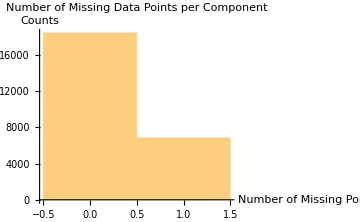

{Missing -> Counts: ,<|0→18427,1→6841|>}

-Graphics-

<|186→<|{FAM138A,RNA}→{{Missing[]},{OK}},{OR4F5,RNA}→{{Missing[]},{OK}},{LOC729737,RNA}→{{2.2946},{OK}},25263,{RNA45S5,RNA}→{{Missing[]},{OK}},{DUX4L,RNA}→{{Missing[]},{OK}}|>,255→<|1|>,11,380→1,400→<|1|>|>
 |  |  |  |

```mathematica
rnaFiltered=FilterMissing[rnaNoiseAdjusted,3/4,Reference-> "255"]
```

#### Create Transcriptome Time Series

We can now create time series for each of the genes. MathIOmica provides functions to facilitate the process, such as CreateTimeSeriespaclet:MathIOmica/ref/CreateTimeSeries and TimeExtractorpaclet:MathIOmica/ref/TimeExtractor. The functions assume an OmicsObject as an input for which times have been used as the sample labels (outer keys).

CreateTimeSeries[omicsObject]  | creates a time series list across an OmicsObject using outer keys as times.
TimeExtractor[omicsObject] | extracts a list of sorted times from an OmicObject's outer keys.

We extract the times for the filtered RNA data using TimeExtractorpaclet:MathIOmica/ref/TimeExtractor:

```mathematica
timesRNA=TimeExtractor[rnaFiltered]
```

{186,255,289,290,292,294,297,301,307,311,322,329,369,380,400}

For each gene we now extract a time series (list of values) corresponding to these times:

```mathematica
timeSeriesRNA=CreateTimeSeries[rnaFiltered]
```

<|{FAM138A,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{OR4F5,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{LOC729737,RNA}→{2.2946,1,4.67694,4.48131,4.95507,1,1.25726,2.14767,1.93219,1,2.58217,2.31301,4.10284,3.80929,1.45471},{DDX11L1,RNA}→{5.91665,4.32081,3.19599,3.64164,2.7327,2.13461,2.17168,3.23429,1.89576,3.0267,4.34004,7.27001,2.01132,9.27701,7.54415},25260,{RNA5-8S5,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{LOC100507412,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{RNA45S5,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{DUX4L,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1}|>
 |  |  |  |

#### Take Log Ratios Compared to Reference in Transcriptome Time Series

Next, we want to use log ratios of expression at any time point compared to a healthy datapoint.

SeriesApplier[function,data] | applies a given function to data, an association of lists, implementing masking for Missing values.

Applying a function to a series with Missing data.

We first use SeriesApplierpaclet:MathIOmica/ref/SeriesApplier to implement the logarithm:

```mathematica
timeSeriesRNALog=SeriesApplier[Log,timeSeriesRNA]
```

<|{FAM138A,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{OR4F5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC729737,RNA}→{0.830556,0,1.54264,1.49992,1.60041,0,0.228935,0.764385,0.658653,0,0.94863,0.838548,1.41168,1.33744,0.374807},{DDX11L1,RNA}→{1.77777,1.46344,1.1619,1.29243,1.00529,0.758282,0.775501,1.17381,0.639619,1.10747,1.46788,1.98376,0.698792,2.22754,2.02077},25260,{RNA5-8S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC100507412,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{RNA45S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{DUX4L,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0}|>
 |  |  |  |

Now we need to compare  to use log ratios of expression at any time point compared to a healthy datapoint. We can use the function SeriesInternalComparepaclet:MathIOmica/ref/SeriesInternalCompare:

SeriesInternalCompare[associationOfLists] | compares each value in each list of associationOfLists to an internal reference value in the list, if the reference point itself is not Missing.

Comparing values in a series to an internal reference point in the series.

option name | default value |  
CompareFunction | (If[MatchQ[Head[#2],Missing],Missing[],(#1- #2)]&) | The function is used by a Query operation on non-missing input data. Namely: Query[All,CompareFunction[#,#[[ComparisonIndex]]]&]@
ComparisonIndex | 1 | List position of list value that will be used as a reference data point.
DeleteRule | {Head, Missing} | DeleteRule allows the customization of how to select values for the reference data point for which its key should be deleted.  The DeleteRule value takes the structure deleteRuleOptionValue={MatchQpaclet:ref/MatchQfirst argument,MatchQpaclet:ref/MatchQsecond argument}.
The MatchQ function referred to here is implemented by SeriesInternalComparepaclet:MathIOmica/ref/SeriesInternalCompare internally, and uses the deleteRuleOptionValue as:
MatchQ[deleteRuleOptionValue[[1]][reference comparison value],deleteRuleOptionValue[[2]]]
The default removes the corresponding key if the value used for reference in the comparison is actually Missing, i.e. the comparison reference point has Head that matches Missing.

Options for SeriesInternalComparepaclet:MathIOmica/ref/SeriesInternalCompare.

We compare every value in each series to the healthy "255" time point, which is the second element in each series:

```mathematica
rnaCompared=SeriesInternalCompare[timeSeriesRNALog,ComparisonIndex->2]
```

<|{FAM138A,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{OR4F5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC729737,RNA}→{0.830556,0,1.54264,1.49992,1.60041,0,0.228935,0.764385,0.658653,0,0.94863,0.838548,1.41168,1.33744,0.374807},{DDX11L1,RNA}→{0.314326,0.,-0.301545,-0.171011,-0.458154,-0.705162,-0.687943,-0.289634,-0.823824,-0.35597,0.00444068,0.520314,-0.764652,0.764095,0.557328},25260,{RNA5-8S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC100507412,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{RNA45S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{DUX4L,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0}|>
 |  |  |  |

#### Take the Norm and Remove Constant Transcriptome Time Series

Next, we normalize each series, using again SeriesApplierpaclet:MathIOmica/ref/SeriesApplier:

```mathematica
normedRNACompared=SeriesApplier[Normalize,rnaCompared]
```

<|{FAM138A,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{OR4F5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC729737,RNA}→{0.218293,0.,0.40545,0.39422,0.420632,0.,0.0601705,0.200902,0.173112,0.,0.249326,0.220394,0.371029,0.351517,0.0985097},{DDX11L1,RNA}→{0.156411,0.,-0.150051,-0.0850959,-0.22798,-0.350893,-0.342324,-0.144124,-0.40994,-0.177133,0.00220971,0.258911,-0.380495,0.380218,0.27733},25260,{RNA5-8S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC100507412,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{RNA45S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{DUX4L,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0}|>
 |  |  |  |

ConstantSeriesClean[dataIn] | removes constant list series from an association of lists.

Removing constant series.

Finally, we use ConstantSeriesCleanpaclet:MathIOmica/ref/ConstantSeriesClean to remove constant series, as we are interested in changing time patterns:

```mathematica
rnaFinalTimeSeries=ConstantSeriesClean[normedRNACompared]
```

Removed series and returning filtered list. If you would like a list of removed keys run the command ConstantSeriesClean[data,ReturnDropped → True].

<|{LOC729737,RNA}→{0.218293,0.,0.40545,0.39422,0.420632,0.,0.0601705,20,0.173112,0.,0.249326,0.220394,0.371029,0.351517,0.0985097},11783|>
 |  |  |  |

### Resampling Transcriptome Data

In addition to the above, we want to create a resampled distribution for the transcriptome dataset prior to classification and clustering. In this subsection we first resample the imported and labeled transcriptome dataset, Then, we carry out the full analysis in this "bootstrap" dataset, to create a set of random time series. This bootstrap distribution of time series will be used to provide the cutoffs used in the time series classification in the following subsection.

#### Resampling the Transcriptome Data

First, we use BootstrapGeneralpaclet:MathIOmica/ref/BootstrapGeneral:

BootstrapGeneral[omicsObject, numberResampled] | performs a resampling of the omicsObject data with replacement, and generates a new association structure with numbering corresponding to the numberResampled of new identities.

We can perform resampling of an OmicsObject to create a bootstrap dataset to be used for statistical considerations.

We create a resampling of 100000 sets:

```mathematica
rnaBootstrap=BootstrapGeneral[rnaLongitudinal,100000]
```

<|186→<|1→{{5.5402},{OK}},2→{{0},{OK}},3→{{0.00246625},{OK}},4→{{12.7439},{OK}},5→{{0},{OK}},99990,99996→{{0.347246},{OK}},99997→{{12.2697},{OK}},99998→{{0},{OK}},99999→{{0},{OK}},100000→{{0},{OK}}|>,255→<|1|>,11,1,400→<|1|>|>
 |  |  |  |

#### Processing the Bootstrap Transcriptome and Creating Bootstrap Time Series

We normalize the transcriptome bootstrap data using the QuantileNormalizationpaclet:MathIOmica/ref/QuantileNormalization function:

```mathematica
rnaBootstrapQuantileNormed=QuantileNormalization[rnaBootstrap,ListIndex-> 1,ComponentIndex-> 1];
```

We use  LowValueTagpaclet:MathIOmica/ref/LowValueTag to tag zero values as Missing[]:

```mathematica
rnaBootstrapZeroTagged=LowValueTag[rnaBootstrapQuantileNormed,0];
```

We next use  LowValueTagpaclet:MathIOmica/ref/LowValueTag again to set all FPKM values <1 to unity:

```mathematica
rnaBootstrapNoiseAdjusted=LowValueTag[rnaBootstrapZeroTagged,1,ValueReplacement-> 1];
```

Next, we filter out data where the reference point "255" is missing and retain data with at least 3/4 points available:

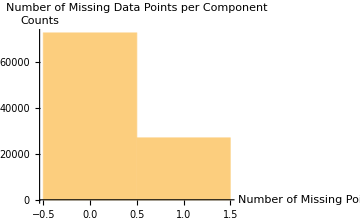

{Missing -> Counts: ,<|0→72929,1→27071|>}

-Graphics-

<|186→<|1→{{4.74683},{OK}},2→{{Missing[]},{OK}},3→{{1},{OK}},4→{{11.6602},{OK}},99992,99997→{{11.2634},{OK}},99998→{{Missing[]},{OK}},99999→{{Missing[]},{OK}},100000→{{Missing[]},{OK}}|>,13,400→<|1|>|>
 |  |  |  |

```mathematica
rnaBootstrapFiltered=FilterMissing[rnaBootstrapNoiseAdjusted,3/4,Reference-> "255"]
```

For each bootstrap member we now extract a time series (list of values) corresponding to the series times:

```mathematica
timeSeriesBootstrapRNA=CreateTimeSeries[rnaBootstrapFiltered]
```

<|1→{4.74683,1,204.567,1,1,1,3.21745,6.86314,1,1,1,1,1,6.62081,1.12378},99998,100000→{Missing[],1,1,1,1,28.9646,1,1,9.1248,1,1,1,1.01897,18.9606,1}|>
 |  |  |  |

We use SeriesApplierpaclet:MathIOmica/ref/SeriesApplier to implement a logarithm:

```mathematica
timeSeriesBootstrapRNALog=SeriesApplier[Log,timeSeriesBootstrapRNA]
```

<|1→{1.55748,0,5.32089,0,0,0,1.16859,1.92616,0,0,0,0,0,1.89022,0.116702},99998,100000→{Missing[],0,0,0,0,3.36607,0,0,2.211,0,0,0,0.0187912,2.94236,0}|>
 |  |  |  |

We compare every value in each series to the healthy "255" time point, which is the second element in each series:

```mathematica
rnaBootstrapCompared=SeriesInternalCompare[timeSeriesBootstrapRNALog,ComparisonIndex->2]
```

<|1→{1.55748,0,5.32089,0,0,0,1.16859,1.92616,0,0,0,0,0,1.89022,0.116702},99998,100000→{Missing[],0,0,0,0,3.36607,0,0,2.211,0,0,0,0.0187912,2.94236,0}|>
 |  |  |  |

Next, we normalize each series, using again SeriesApplierpaclet:MathIOmica/ref/SeriesApplier:

```mathematica
normedBootstrapRNACompared=SeriesApplier[Normalize,rnaBootstrapCompared]
```

<|1→{0.248127,0.,0.84769,0.,0.,0.,0.186172,0.306864,0.,0.,0.,0.,0.,0.301137,0.0185922},99998,100000→{Missing[],0.,0.,0.,0.,5,0.,0.,0.00376754,0.589928,0.}|>
 |  |  |  |

Finally, we use ConstantSeriesCleanpaclet:MathIOmica/ref/ConstantSeriesClean to remove constant series, as we are interested in changing time patterns:

```mathematica
rnaBootstrapFinalTimeSeries=ConstantSeriesClean[normedBootstrapRNACompared]
```

Removed series and returning filtered list. If you would like a list of removed keys run the command ConstantSeriesClean[data,ReturnDropped → True].

<|1→{0.248127,0.,0.84769,0.,0.,0.,0.186172,0.306864,0.,0.,0.,0.,0.,0.301137,0.0185922},99965,100000→{Missing[],0.,0.,0.,0.,5,0.,0.,0.00376754,0.589928,0.}|>
 |  |  |  |

### Classification of Transcriptome Time Series

In this subsection we will classify the transcriptome time series based on patterns in the series. For the classification we will use TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification.

TimeSeriesClassification[data, setTimes] | takes a data association (or list of lists) of values corresponding to intensities collected over time and classifies the values into classes (groups) that show distinct similar temporal patterns. TimeSeriesClassification takes as inputs:
data | Association with series as values, or a list of series, where the series contain information regarding time intensities/observations. Each series may include Missingpaclet:ref/Missing data points and may be entered as list of N signal intensities corresponding one-to-one to the N setTimes with Missingpaclet:ref/Missing inserted appropriately if the data is absent, {X_1=X(t_1),X_2=X(t_2),...,X_N=X(t_N)}. Alternatively, each series data may be a list of pairs of values {{t_1,X_1},{t_2,X_2},. ..,{t_N,X_N}} for only existing measurements.
setTimes | A global complete set of all possible N times during which all data series could have been collected in the window of the experiment, including times for which no values were reported or are missing, {t_1,t_2,...,t_N}.

Classifying a set of time series based on temporal behavior.

option name | default value |  
AutocorrelationCutoffs | {0} | Cutoffs, for "Autocorrelation" and "InterpolatedAutocorrelation" methods, for different lags that will be used to filter out data series for which the lags are not within cutoffs. The list length corresponds to cuttofs at different lags, with the ith lag cutoff provided as the ith index, i.e. ρ_c={ρ_c1,ρ_(c2,),...,ρ_(ci,),..., ρ_jk} up to k, where 1≤k≤  n, and typically n=Floor[Length[setTimes]/2]. The classification will only consider lags up to the length of the list provided. The cutoffs are user-provided and typically calculated through simulation.
AutocorrelationLogic | False | Option to return the autocorrelation logic list for each signal, with the default set to Falsepaclet:ref/False. If set to True, a logic vector is returned indicating whether or not at a particular lag the autocorrelation for a signal is above or below the AutocorrelationCutoffs.
AutocorrelationOptions | {UpperFrequencyFactor →  1} | Options that are used by the internal Autocorrelation function in the case that  the Method→ "Autocorrelation" is set.
InterpolationDeltaT | "Auto" | Time step used to grid the time window over which calculations will be performed. If set to "Auto" the step will correspond to dividing the span of the interval into a number of equal steps equal to the number of input time points.
InterpolationOptions | {} | Options list for the internal Interpolation function used to interpolate between data points that have Missing values or uneven spacing.
LombScargleCutoff | 0 | Cutoff value for "LombScargle" method, for filtering the highest intensity observed in the power spectrum. The cutoff is user-provided and typically calculated through simulation. 
LombScargleOptions | {PairReturn→  False,NormalizeIntensities→ True} | Options that are used by the internal LombScargle function if the case that the Method→ "LombScargle" is set.
Method | "LombScargle" | Selection of which algorithm to use in the classification scheme.
ReturnAllSpikes | False | Option whether each signal may maintain unique membership to each spike class, or be allowed to belong to multiple classes. Used in "Autocorrelation" and "InterpolatedAutocorrelation" methods. If set to False, first spike maxima are classified, and only signals found not to belong to spike maxima are then considered for membership in the spike minima class.
ReturnData | True | If set to True will return input keys to data associations in the classification. If set to False will only return the keys of the input data in the classification.
ReturnModels | False | Whether to return the models as well as the classification information for the input data. The data is returned as an association with the  key "TimeSeriesClasses" for classification groups and one of the following: (i) "Models" for model-based methods, (ii) "LombScargle" for periodograms in the "LombScargle" method, (iii) "Autocorrelations" for autocorrelation based methods.
SpikeCutoffs | <|1 →{.99,-99}, 2 → {.99,-99}|> | Association with number, n, of data points as keys, and values corresponding to cutoffs, in the form <|n→ {Maximum Spike Cutoff_n,Minimum Spike Cutoff_n}|> used to call spike maxima and minima for a time series with this number of datapoints. The values are provided by the user depending on data approach based on simulation. The default values are only place-holders and should be replaced by real values. The association must have corresponding keys for all lengths of input datasets, so that Keys[OptionValue[SpikeCutoffs]]∈{Possible lengths of numeric data}. ,  i.e. all possible lengths of series constructed by excluding Missingpaclet:ref/Missing or other non-numeric values).

Options for TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification.

TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification uses multiple methods to classify data. The periodogram/autocorrelation methods used use cutoffs from simulation/user-provided values, to assess class membership based on statistical significance. In this tutorial we will use the "LombScargle" method, to classify data based on a Lomb-Scargle computation of a periodogram. The data is classified based into classes major (highest intensity) frequencies based on the generated periodogram for a signal, when the intensity of this frequency is above an intensity threshold cutoff. Additionally, data that displays spikey behavior in the real intensity, that is not classified into any frequency classes, is classified as a SpikeMaximum or SpikeMinimum if the spike is higher or lower respectively than what one would expect from a random signal.

Method | Description
"LombScargle" | Classification based on periodograms (power spectra) generated by a Lomb-Scargle computation as implemented internally by the LombScarglepaclet:MathIOmica/ref/LombScargle function. The data is classified into classes of major (highest intensity)  frequencies and spikes (maxima or minima in real signal intensity), depending on cutoffs typically provided by simulation and passed to the function by the LombScargleCutoffs and SpikeCutoffs option values. The returned {computed classification vector} for this method is the intensity list of the periodogram for each signal.
"Autocorrelation" | Classification based on autocorrelations generated by a Lomb-Scargle approach using an inverser Fourier transform of spectral intensities, as implemented through the Autocorrelationpaclet:MathIOmica/ref/Autocorrelation function. The data is classified into autocorrelations at different lags and spikes (maxima or minima) classes, depending on cutoffs typically provided by simulation. The returned {computed classification vector} for this method is the autocorrelation list for each signal.
"InterpolatedAutocorrelation" | Classification based on autocorrelations generated directly in time, with Missingpaclet:ref/Missing data handled through interpolation. The data is classified into autocorrelations at different lags and spikes (maxima or minima) classes depending on cutoffs typically provided by simulation. The returned {computed classification  vector} for this method is the autocorrelation list for each signal.
"TimeSeriesModelAggregate" | Classification based on model fitting of time series through TimeSeriesModelFitpaclet:ref/TimeSeriesModelFit and all available models therein. The data is classified into aggregate model classes. The returned {computed classification vector} for this method is the actual input signal.
"TimeSeriesModelDetailed" | Classification based on model fitting of time series through TimeSeriesModelFitpaclet:ref/TimeSeriesModelFit and all available models therein. The data is classified into model classes based on individual model degree parameters.  The returned {computed classification vector} for this method is the "BestFitParameters" for the model fit. If this list is empty an integer list is returned {token integer} - this is used in subsequent clustering applications.

Methods for TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification.

To create the cutoffs for the classification we will first use the bootstrap time series set created in the previous subsection, and QuantileEstimatorpaclet:MathIOmica/ref/QuantileEstimator.

QuantileEstimator[data, timepoints] | obtains the quantile estimator following bootstrap for time series.  It takes as inputs:
       | data | Association or list with series as values, from which to generate a distribution.
       | timepoints | Timepoints over which the time series run.

Estimating  the quantile value that can be used as a cutoff for classification of time series based on bootstrap simulations.

option name | default value |  
AutocorrelationOptions | {} | Specific options when calculating autocorrelations for the time series.
InterpolationDeltaT | "Auto" | Time step used to grid the time window over which calculations will be performed. If set to "Auto" the step will correspond to dividing the span of the interval into a number of equal steps equal to the number of input time points.
InterpolationOptions | {} | Options list for the internal Interpolation function used to interpolate between data points that have Missing values or uneven spacing.
LombScargleOptions | {PairReturn →  False,NormalizeIntensities→ True} | Specific options when calculating LombScargle periodograms for the time series.
Method | "LombScargle" | Method of calculation. Choices include one of the following: {"LombScargle","Autocorrelation", "InterpolatedAutocorrelation","Spikes"}
QuantileValue | 0.95 | Which quantile to extract.

Options for QuantileEstimatorpaclet:MathIOmica/ref/QuantileEstimator.

Depending on the cutoffs we would like to generate, we select the appropriate Method (also considering the Method that the downstream TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification will use).

Method | Description
"Autocorrelation" | List of values corresponding to selected quantile of autocorrelations, with the ith lag quantile provided as the ith index, i.e. ρ_c={ρ_c1,ρ_(c2,),...,ρ_(ci,),..., ρ_ck} up to k lags, where 1≤ k ≤ n, and typically n=Floor[Length[timepoints]/2].  The method utilizes the Autocorrelationpaclet:MathIOmica/ref/Autocorrelation function internally.
"InterpolatedAutocorrelation" | List of values corresponding to selected quantile for autocorrelations, with the ith lag quantile provided as the ith index, i.e. ρ_c={ρ_c1,ρ_(c2,),...,ρ_(ci,),..., ρ_ck} up to k lags, where 1≤ k ≤ n, and typically n=(Length[timepoints]-1). The method utilizes an Interpolation followed by a CorrelationFunction implementation to compute autocorrelations, i.e. missing data or uneven sampling is handled by data interpolation.
"LombScargle" | Single value corresponding to selected quantile of maximum peak intensity of periodogram. The method utilizes the LombScarglepaclet:MathIOmica/ref/LombScargle function internally.
"Spikes" | Association with number, n, of data points as keys, and values corresponding to quantiles for maxima and minima of the series, in the form <|n→ {Maximum Spike Quantile_n,Maximum Spike Quantile_n}|> . The keys are generated automatically so that so that Keys[output]∈{Possible lengths of numeric data}. ,  i.e. all possible lengths of input series constructed by excluding Missing or other non-numeric values).

Method selection and output for QuantileEstimatorpaclet:MathIOmica/ref/QuantileEstimator.

The default output for TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification is an Associationpaclet:ref/Association with outer keys being the classification classes,  inner keys being the class members, and each class member value being a list of {{computed classification vector}, {input data list}}. The general output structure is for M output classes of each having m_i members:

<| Class_1 →  <|Member_11→ {{classification vector_11},{input data vector_11}}, Member_12→  {{classification vector_12},{input data vector_12}},..., Member_(1 m_1)→  {{classification vector_(1 m_1)},{input data vector_(1 m_1)}}|>,Class_2 →  <|Member_21->{{classification vector_21},{input data vector_21}},Member_22->{{classification vector_22},{input data vector_22}},...,Member_(2 m_2)→  {{classification vector_(2 m_2)},{input data vector_(2 m_2)}}|>, ..., Class_M →  <|Member_M1->{{classification vector_M1},{input data vector_M1}},Member_M2->{{classification vector_M2},{input data vector_M2}},...,Member_Mm_M→  {{classification vector_Mm_M},{input data vector_Mm_M}}|>|>

Before we classify our transcriptome data, we estimate for the "LombScargle" Method a 0.95 quantile cutoff from the bootstrap transcriptome data:

```mathematica
q95RNA=QuantileEstimator[rnaBootstrapFinalTimeSeries,timesRNA]
```

0.860232

Next, we estimate the "Spikes" 0.95 quantile cutoff from the bootstrap transcriptome data:

```mathematica
q95RNASpikes=QuantileEstimator[rnaBootstrapFinalTimeSeries,timesRNA,Method-> "Spikes"]
```

<|14→{0.884016,-0.348069},15→{0.858813,-0.337635}|>

Now we can classify the transcriptome time series data based on these cutoffs:

```mathematica
rnaClassification=TimeSeriesClassification[rnaFinalTimeSeries,timesRNA,LombScargleCutoff-> q95RNA,SpikeCutoffs->q95RNASpikes]
```

Method → "LombScargle"

<|SpikeMax→<|{ATAD3C,RNA}→{{0.0855374,0.204135,0.219303,0.378496,0.5849,0.346012,0.545735},{0.,0.,0.,0.,7,0.,0.,0.075919,0.}},821|>,7,f7→<|1|>|>
 |  |  |  |

The default output for TimeSeriesClassification is an Association with outer keys being the classification classes,  inner keys being the class members, and each class member value being a list of {{computed classification vector}, {input data list}}. The general output structure is for M output classes of each having m_i members:

<| Class_1 →  <|Member_11→ {{classification vector_11},{input data vector_11}}, Member_12→  {{classification vector_12},{input data vector_12}},..., Member_(1 m_1)→  {{classification vector_(1 m_1)},{input data vector_(1 m_1)}}|>,Class_2 →  <|Member_21->{{classification vector_21},{input data vector_21}},Member_22->{{classification vector_22},{input data vector_22}},...,Member_(2 m_2)→  {{classification vector_(2 m_2)},{input data vector_(2 m_2)}}|>, ..., Class_M →  <|Member_M1->{{classification vector_M1},{input data vector_M1}},Member_M2->{{classification vector_M2},{input data vector_M2}},...,Member_Mm_M→  {{classification vector_Mm_M},{input data vector_Mm_M}}|>|>

If we want the classes produced, we can query the keys:

```mathematica
Keys[rnaClassification]
```

{SpikeMax,SpikeMin,f1,f2,f3,f4,f5,f6,f7}

For the number of members in each class we have:

```mathematica
Query[All,Length]@rnaClassification
```

<|SpikeMax→822,SpikeMin→5963,f1→116,f2→3,f3→30,f4→128,f5→35,f6→13,f7→61|>

We can obtain the membership list in any class of interest:

```mathematica
Query["f1",Keys]@rnaClassification
```

{{PADI4,RNA},{AHDC1,RNA},{CCDC28B,RNA},{AGO1,RNA},{JAK1,RNA},{C1orf52,RNA},{IARS2,RNA},{URB2,RNA},{HSPA14,RNA},{WBP1L,RNA},{PDZD8,RNA},{LOC102288414,RNA},{TRMT112,RNA},{DRAP1,RNA},{CDK2AP2,RNA},{FAM168A,RNA},{FLI1,RNA},{EFCAB4B,RNA},{EMG1,RNA},{NDUFA12,RNA},{ELK3,RNA},{SSH1,RNA},{C12orf49,RNA},{IPO5,RNA},{TMCO3,RNA},{KIAA0586,RNA},{JKAMP,RNA},{PCNX,RNA},{EHD4,RNA},{CLPX,RNA},{AAGAB,RNA},{RCCD1,RNA},{FAM173A,RNA},{LINC00921,RNA},{ZC3H7A,RNA},{GLG1,RNA},{MBTPS1,RNA},{TNFRSF13B,RNA},{ZNF207,RNA},{ACLY,RNA},{PSME3,RNA},{TEX2,RNA},{PRKCA,RNA},{ATP9B,RNA},{MBP,RNA},{ADNP2,RNA},{HOOK2,RNA},{EMR3,RNA},{SDHAF1,RNA},{ZNF529,RNA},{RPL18,RNA},{CTU1,RNA},{GEMIN6,RNA},{GMCL1,RNA},{COA5,RNA},{MRPS9,RNA},{GTF3C3,RNA},{NDUFS1,RNA},{RALGAPA2,RNA},{LOC284801,RNA},{SAMHD1,RNA},{SERINC3,RNA},{USP25,RNA},{RUNX1,RNA},{DSCR3,RNA},{THAP7,RNA},{MAPK1,RNA},{PITPNB,RNA},{EWSR1,RNA},{NPTXR,RNA},{TCF20,RNA},{ARPC4,RNA},{STT3B,RNA},{SNRK-AS1,RNA},{CCDC12,RNA},{PRKAR2A,RNA},{GSK3B,RNA},{PTPLB,RNA},{DNAJC13,RNA},{LRCH3,RNA},{KLF3,RNA},{ANTXR2,RNA},{GPRIN3,RNA},{INPP4B,RNA},{PTGER4,RNA},{NNT,RNA},{CCDC125,RNA},{POC5,RNA},{ERAP1,RNA},{TBC1D22B,RNA},{HACE1,RNA},{SYNJ2,RNA},{CYTH3,RNA},{STAG3L1,RNA},{STAG3L3,RNA},{MTERF,RNA},{MBLAC1,RNA},{TRIM56,RNA},{AHCYL2,RNA},{RNF122,RNA},{ADAM9,RNA},{PRKDC,RNA},{AGO2,RNA},{ERMP1,RNA},{KDM4C,RNA},{FOCAD,RNA},{CEP78,RNA},{RC3H2,RNA},{GTF3C4,RNA},{ZRSR2,RNA},{PDK3,RNA},{CASK,RNA},{DDX3X,RNA},{TIMP1,RNA},{ARHGEF6,RNA},{IDS,RNA}}

We may also want to know what these frequencies correspond to. The "LombScargle" method uses a LombScarglepaclet:MathIOmica/ref/LombScargle transformation.

LombScargle[data, setTimes] | calculates the Lomb-Scargle power spectrum for time series data that runs over specified setTimes. It takes as input:
       | data | Time series (data as a list; list may be the value of a single key in an association). The series may include Missing data points. Data may be entered as list of N signal intensities corresponding one-to-one to the N setTimes with Missing inserted appropriately if the data is absent, {X_1=X(t_1),X_2=X(t_2),...,X_N=X(t_N)}. Alternatively, the data may be a list of pairs of values {{t_1,X_1},{t_2,X_2},. ..,{t_N,X_N}} for only existing measurements.
       | setTimes | A complete set of all possible N times during which data could have been collected in the window of the experiment, including times for which no data was collected,{t_1,t_2,...,t_N}.

Calculating the power spectrum of a (possibly unevenly sampled) time series.

option name | default value |  
FrequenciesOnly | False | Whether to return only the computation frequencies. An association of frequencies "f" ordered from low to high by index i is returned in the form:
<|"f1"→ frequency_1,"f2"→ frequency_2, ...,"fi" → frequency_(i,...,)"fn"→ frequency_n|>
NormalizeIntensities | False | Whether the intensities list should be normalized or not.
OversamplingRate | 1 | Rate at which to oversample the time series using zero-padding.
PairReturn | False | Whether data should be returned as {frequency list,intensity list} or as pairs: {{frequency1,intensity1}, {frequency2, intensity2},...,{frequencyN,intensityN}.
UpperFrequencyFactor | 1 | Value ≥ 1,  by which to scale the upper Nyquist cutoff frequency and increase spectral resolution.

Options for LombScarglepaclet:MathIOmica/ref/LombScargle.

To obtain the possible frequencies we simply run LombScarglepaclet:MathIOmica/ref/LombScargle over the desired times for one of the time series and set the FrequenciesOnly option to Truepaclet:ref/True:

```mathematica
LombScargle[rnaFinalTimeSeries[[1]],timesRNA,FrequenciesOnly-> True]
```

<|f1→0.00500668,f2→0.0104306,f3→0.0158545,f4→0.0212784,f5→0.0267023,f6→0.0321262,f7→0.0375501|>

## Proteomic Data

### Importing OmicsObject Proteome Data

We now import the proteomics data example (for details on how to import such data please refer to DataImporterpaclet:MathIOmica/ref/DataImporter, DataImporterDirectpaclet:MathIOmica/ref/DataImporterDirect, DataImporterDirectLabeledpaclet:MathIOmica/ref/DataImporterDirectLabeled and OmicsObjectCreatorpaclet:MathIOmica/ref/OmicsObjectCreator documentation).

We import the proteomics OmicsObject MathIOmica example:

```mathematica
proteinExample=Get[FileNameJoin[{ConstantMathIOmicaExamplesDirectory,"proteinExample"}]]
```

<|7→<|{A0AVT1,Protein}→{{0.937},{17}},{A0FGR8,Protein}→{{1.073},{24}},{A0MZ66,Protein}→{{1.059},{9}},5219,{Q9Y6I4,Protein}→Missing[],{Q9Y6I9,Protein}→Missing[],{Q9Y6X3,Protein}→Missing[]|>,9→<|1|>,9,20→1,21→<|1|>|>
 |  |  |  |

There are multiple samples given by the outer associations. We can use Query to get any data. For example we can get the outer keys:

```mathematica
Query[Keys]@proteinExample
```

{7,9,10,11,14,12,13,15,16,17,19,20,21}

We notice that sample 8 is missing - this is because it was used as a reference in the proteomics experiment. Point 18 is missing as there was no sample for that time point. We will address this in the next section.

We can get the expression raw data from any sample and entry. For example, the 14^th and 214^th entries in sample 12:

```mathematica
Query["12",{14,22}]@proteinExample
```

<|{A5PLN9,Protein}→{{1.057},{3}},{A6NGU5,Protein}→Missing[]|>

The keys correspond to UniProt accessions, and have been tagged with a "Protein" label as well. The  values of all the keys/IDs correspond to {{measurements},{metadata}}, and in this particular example:  {{relative intensity compared to reference},{number of unique peptides identified for the given protein}}.

The measurement for each protein is a relative intensity, i.e. the ratio of the value for the protein compared to the reference timepoint that has been chosen as the healthy sample "8", day "255" (in the experiment this was TMT reporter with 126 amu). The last list, the "metadata", in the proteomics OmicsObject was chosen to be the number of unique peptides identified for the given protein.

##### Additional Information: Gene Translation

As an aside, let us consider the form of the protein identifiers. MathIOmica can perform basic GeneTranslationpaclet:MathIOmica/ref/GeneTranslation going from one kind of identifier to another, using GetGeneDictionarypaclet:MathIOmica/ref/GetGeneDictionary:

GeneTranslation[inputIDList,targetIDList,geneDictionary] | uses geneDictionary to convert inputIDList IDs to different annotations as indicated by targetIDList. It takes for inputs:
inputIDList | List of n IDs (strings) to be converted in the form {inputID_(1,)inputID_2,...,inputID_n}
targetIDList | List of target identifier strings, as used in the gene geneDictionary,{target ID_1,targetID_2,...target ID_k}, e.g. {"UniProt ID","Gene Symbol"}. Can also be provided as a single string for only one kind of IDs.
geneDictionary | Gene dictionary to base translation on in the form generated by GetGeneDictionarypaclet:MathIOmica/ref/GetGeneDictionary.
GetGeneDictionary[] | creates an ID/accession dictionary from a UCSC table search - typically of gene annotations. GetGeneDictionary uses MathIOmica data for the annotations..

Translating gene identifiers using a gene dictionary.

We use GetGeneDictionary to define a gene dictionary:

```mathematica
geneDictionary=GetGeneDictionary[]
```

<|human→<|UCSC ID→{uc001aaa.3,uc010nxr.1,uc010nxq.1,uc001aal.1,uc001aaq.2,uc001aar.2,uc001aau.3,uc021oeh.1,121567,uc022cfk.1,uc031tkn.1,uc022cgh.1,uc022cha.1,uc022chb.1,uc022chc.1,uc022che.1,uc022cpe.1},6,HGU…x ID→1|>|>
 |  |  |  |

The current version of the gene dictionary has accessions for the following identifiers:

```mathematica
Query[All,Keys]@geneDictionary
```

<|human→{UCSC ID,UniProt ID,Gene Symbol,RefSeq ID,NCBI Protein Accession,Ensembl ID,KEGG Gene ID,HGU133Plus2 Affymetrix ID}|>

We can now use GeneTranslation (setting the optional InputID to "UniProt ID") to convert our example "UniProt ID" accessions to "Gene Symbol":

```mathematica
GeneTranslation[{"A5PLN9","A6NGU5"},{"Gene Symbol"},geneDictionary,InputID-> {"UniProt ID"}]
```

<|Gene Symbol→<|A5PLN9→{TRAPPC13},A6NGU5→Missing[]|>|>

We note that an ID might not necessarily be annotated across all databases, as in the above example.

### Processing of Proteome Data

We will next preprocess the imported proteome data. We will first perform a transformation on the data towards a normal distribution, then we will re-label the samples with real time and carry out filtering for unique peptides present in each protein identification, as well as for missing data. Finally, we will create the proteomics time series or relative intensities compared to the healthy reference point for each protein.

#### Power Transformation, Labeling and Filtering

##### Data Power Transformation

To make the data comparable across time points, and as close to a normal distribution as possible for each sample, we normalize each time point /sample by using ApplyBoxCoxTransformpaclet:MathIOmica/ref/ApplyBoxCoxTransform.

ApplyBoxCoxTransform[data] | for a given data set, computes the Box-Cox transformation at the maximum likelihood λ parameter.

Applying a power transformation (Box-Cox) for an optimized parameter for each dataset.

option name | default value |  
ListIndex | Missing[] | Selection of which list to use in the OmicsObject input.
ComponentIndex | Missing[] | Selection of which component of a list to use in the OmicsObject input.
HorizontalSelection | False | Horizontal selection across components for a single level association with multi-list values.

Options for ApplyBoxCoxTransformpaclet:MathIOmica/ref/ApplyBoxCoxTransform.

We apply a Box-Cox transformation to the proteomics data measurement in the OmicsObject, which is in the first list first component for each identifier. The optimized λ̂ parameter for each sample is printed out for reference:

```mathematica
transformedProteinData=ApplyBoxCoxTransform[proteinExample,ListIndex-> 1,ComponentIndex-> 1]
```

Calculated Box-Cox parameter λ̂ = -0.152638

Calculated Box-Cox parameter λ̂ = -0.177086

Calculated Box-Cox parameter λ̂ = -0.421581

Calculated Box-Cox parameter λ̂ = -0.292287

Calculated Box-Cox parameter λ̂ = -0.432042

Calculated Box-Cox parameter λ̂ = 0.346673

Calculated Box-Cox parameter λ̂ = 0.368061

Calculated Box-Cox parameter λ̂ = 0.0834074

Calculated Box-Cox parameter λ̂ = 0.13413

Calculated Box-Cox parameter λ̂ = 0.166336

Calculated Box-Cox parameter λ̂ = 0.0866284

Calculated Box-Cox parameter λ̂ = -0.199247

Calculated Box-Cox parameter λ̂ = -0.221778

<|7→<|{A0AVT1,Protein}→{{-0.0653962},{17.}},{A0FGR8,Protein}→{{0.0700809},{24.}},5221,{Q9Y6I9,Protein}→Missing[],{Q9Y6X3,Protein}→Missing[]|>,11,21→<|{A0AVT1,Protein}→{{-21},1},5223,1|>|>
 |  |  |  |

We can plot the data to see what the resulting distributions look like:

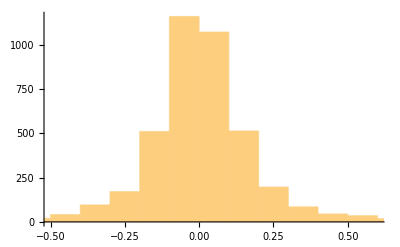
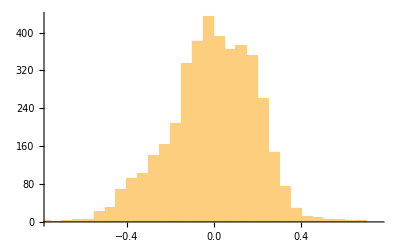
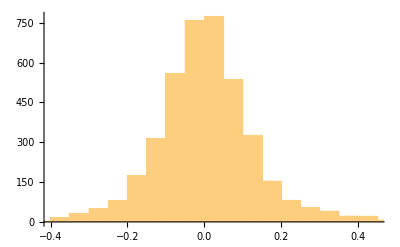
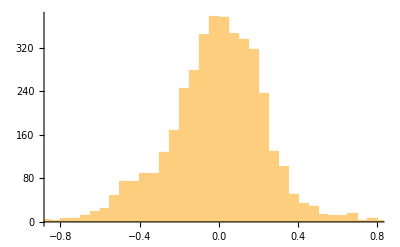
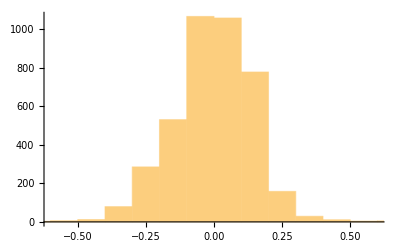
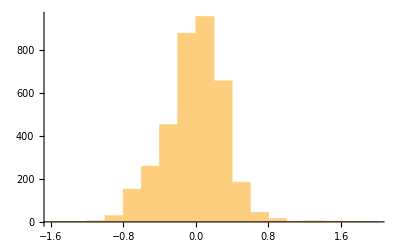
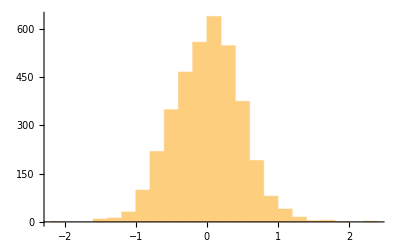
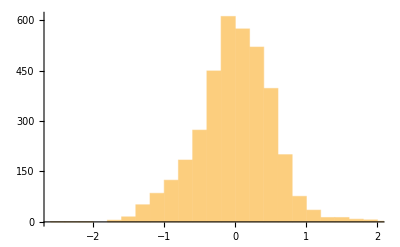
<|7→-Graphics-,9→-Graphics-,10→-Graphics-,11→-Graphics-,14→-Graphics-,12→-Graphics-,13→-Graphics-,15→-Graphics-,16→-Graphics-,17→-Graphics-,19→-Graphics-,20→-Graphics-,21→-Graphics-|>

```mathematica
Histogram[#]&/@(Query[All,Values,1,1]@transformedProteinData)
```

##### Re-labeling Samples with Times

As with the transcriptome, we notice that the sample numberings do not correspond to actual days, so we may adjust using the sampleToDays association created before and reproduced here for reference:

```mathematica
sampleToDays= <|"7"->"186","8"->"255","9"->"289","10"->"290","11"->"292","12"->"294","13"->"297","14"->"301","15"->"307","16"->"311","17"->"322","18"->"329","19"->"369","20"->"380","21"->"400"|>;
```

We can now do a KeyMap to rename the outer keys:

```mathematica
proteinLongitudinal=KeyMap[sampleToDays,transformedProteinData]
```

<|186→<|{A0AVT1,Protein}→{{-0.0653962},{17.}},{A0FGR8,Protein}→{{0.0700809},{24.}},{A0MZ66,Protein}→{{0.057075},{9.}},5220,{Q9Y6I9,Protein}→Missing[],{Q9Y6X3,Protein}→Missing[]|>,11,400→<|1|>|>
 |  |  |  |

Now let's check the timepoints in this dataset:

```mathematica
timesProteinRawData=TimeExtractor[proteinLongitudinal]
```

{186,289,290,292,294,297,301,307,311,322,369,380,400}

We notice a small complication: there are two timepoints missing, compared to the transcriptome: (i) the reference time point "255" does not appear explicitly in our computation (corresponding to a zero value about which other timepoints are computed for proteins with at least 2 unique peptides). (ii) there is no sample for day "329".

We can use the ConstantAssociatorpaclet:MathIOmica/ref/ConstantAssociator function to append these to the transformed data. Timepoints "255" (zero measurement assumed to have at least 2 unique peptides available per protein) and "329", assumed to be Missing data:

```mathematica
proteinLongitudinalEnlarged=ConstantAssociator[proteinLongitudinal,<|"255"-> {{0},{2}},"329"-> Missing[]|>]
```

<|186→<|{A0AVT1,Protein}→{{-0.0653962},{17.}},{A0FGR8,Protein}→{{0.0700809},{24.}},{A0MZ66,Protein}→{{0.057075},{9.}},5220,{Q9Y6I9,Protein}→Missing[],{Q9Y6X3,Protein}→Missing[]|>,13,329→<|1|>|>
 |  |  |  |

We can now check the timepoints again:

```mathematica
timesProtein=TimeExtractor[proteinLongitudinalEnlarged]
```

{186,255,289,290,292,294,297,301,307,311,322,329,369,380,400}

##### Filter Unique Peptides

Typically, proteomics data from mass spectrometry is filtered to retain only identifications of proteins that are supported by at least 2 unique peptides having been identified per protein. We can use FilteringFunctionpaclet:MathIOmica/ref/FilteringFunction to implement the filtering:

FilteringFunction[omicsObject, cutoff] | filters OmicsObject data by a chosen comparison (by default greatr or equal) to a cutoff.

FilteringFunction can be used to filter data in an OmicsObject.

option name | default value |  
ListIndex | Missing[] | Selection of which list to use in the OmicsObject input.
ComponentIndex | Missing[] | Selection of which component of a list to use in the OmicsObject input.
SelectionFunction | GreaterEqual | Selection of comparison to use for filtering.

Options for FilteringFunctionpaclet:MathIOmica/ref/FilteringFunction.

We filter out proteomics data with less than 2 unique peptides per protein. The unique peptides is reported as the second list, first component in the OmicsObject values in this case:

```mathematica
proteinUnique=FilteringFunction[proteinLongitudinalEnlarged,2,ListIndex-> 2,ComponentIndex-> 1]
```

<|186→<|{A0AVT1,Protein}→{{-0.0653962},{17.}},{A0FGR8,Protein}→{{0.0700809},{24.}},{A0MZ66,Protein}→{{0.057075},{9.}},5220,{Q9Y616,Protein}→Missing[],{Q9Y6X3,Protein}→Missing[]|>,13,329→<|1|>|>
 |  |  |  |

##### Filter Data

We will next remove values that have been tagged as Missing[], retaining data that have at least 3/4 data points available across all samples. Here we use the function FilterMissingpaclet:MathIOmica/ref/FilterMissing:

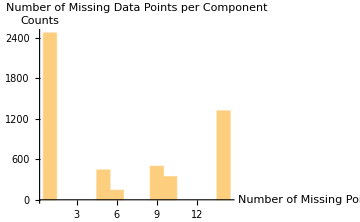

{Missing -> Counts: ,<|1→2475,5→443,6→143,9→499,10→345,14→1320|>}

-Graphics-

<|186→<|{A0AVT1,Protein}→{{-0.0653962},{17.}},{A0FGR8,Protein}→{{0.0700809},{24.}},2471,{Q9Y6W5,Protein}→{{-0.0514946},{14.}},{Q9Y6Y8,Protein}→{{-0.026397},{10.}}|>,13,329→<|1|>|>
 |  |  |  |

```mathematica
filteredProteinData=FilterMissing[proteinUnique,3/4]
```

#### Create Proteome Time Series

We can now create time series for each of the proteins.

For each protein we now extract a time series (list of values) corresponding to these times:

```mathematica
timeSeriesProtein=CreateTimeSeries[filteredProteinData]
```

<|{A0AVT1,Protein}→{-0.0653962,0,0.00299471,-0.0348449,-0.0182123,0.0627073,3,0.0829594,0.0689856,Missing[],-0.050132,-0.137674,-0.0120888},2473,1|>
 |  |  |  |

#### Take the Norm and Remove Constant Proteome Time Series

Next, we normalize each protein series, using SeriesApplierpaclet:MathIOmica/ref/SeriesApplier:

```mathematica
normedProteinAll=SeriesApplier[Normalize,timeSeriesProtein]
```

<|{A0AVT1,Protein}→{-0.205122,0.,0.00939321,-0.109294,-0.0571245,0.196687,0.529638,0.0740093,-0.539241,0.26021,0.21638,Missing[],-0.157244,-0.431828,-0.0379175},2473,{Q9Y6Y8,Protein}→{-0.0502772,0.,0.0961208,0.0848518,0.207372,0.188143,3,0.134835,-0.133348,Missing[],-0.185135,0.,-0.369519}|>
 |  |  |  |

Finally, we use ConstantSeriesCleanpaclet:MathIOmica/ref/ConstantSeriesClean to remove constant series, as we are interested in changing time patterns:

```mathematica
proteinFinalTimeSeries=ConstantSeriesClean[normedProteinAll]
```

<|{A0AVT1,Protein}→{-0.205122,0.,0.00939321,-0.109294,-0.0571245,0.196687,0.529638,0.0740093,-0.539241,0.26021,0.21638,Missing[],-0.157244,-0.431828,-0.0379175},2473,{Q9Y6Y8,Protein}→{-0.0502772,0.,0.0961208,0.0848518,0.207372,0.188143,3,0.134835,-0.133348,Missing[],-0.185135,0.,-0.369519}|>
 |  |  |  |

### Resampling Proteome Data

In addition to the above, we want to create a resampled distribution for the proteome dataset prior to classification and clustering. In this subsection we first resample the imported and labeled proteome dataset, Then, we carry out the full analysis in this "bootstrap" dataset, to create a set of random proteome time series. This bootstrap distribution of time series will be used to provide the cutoffs used in the time series classification in the following subsection.

#### Resampling the Proteome Data

We create a resampling of 100000 sets:

```mathematica
proteinBootstrap=BootstrapGeneral[proteinExample,100000]
```

<|7→<|1→{{1.061},{1}},2→{{1.053},{10}},3→Missing[],4→{{1.13},{8}},5→Missing[],6→{{0.888},{1}},7→Missing[],99987,99995→{{1.027},{15}},99996→{{0.926},{6}},99997→Missing[],99998→{{0.993},{1}},99999→Missing[],100000→{{1.325},{1}}|>,11,21→<|1|>|>
 |  |  |  |

#### Processing the Bootstrap Proteome and Creating Bootstrap Time Series

We apply a Box-Cox transformation to the bootstrap set proteomics data measurement in the OmicsObject, which is in the first list first component for each identifier. The optimized λ̂ parameter for each sample is printed out for reference:

```mathematica
transformedProteinBootstrapData=ApplyBoxCoxTransform[proteinBootstrap,ListIndex-> 1,ComponentIndex-> 1]
```

Calculated Box-Cox parameter λ̂ = -0.150171

Calculated Box-Cox parameter λ̂ = -0.222817

Calculated Box-Cox parameter λ̂ = -0.368798

Calculated Box-Cox parameter λ̂ = -0.28793

Calculated Box-Cox parameter λ̂ = -0.47914

Calculated Box-Cox parameter λ̂ = 0.340883

Calculated Box-Cox parameter λ̂ = 0.366836

Calculated Box-Cox parameter λ̂ = 0.0673515

Calculated Box-Cox parameter λ̂ = 0.13962

Calculated Box-Cox parameter λ̂ = 0.156325

Calculated Box-Cox parameter λ̂ = 0.100479

Calculated Box-Cox parameter λ̂ = -0.186707

Calculated Box-Cox parameter λ̂ = -0.215203

<|7→<|1→{{0.0589494},{1.}},2→{{0.0514435},{10.}},3→Missing[],4→{{0.121103},{8.}},5→Missing[],99991,99997→Missing[],99998→{{-0.00702832},{1.}},99999→Missing[],100000→{{0.275549},{1.}}|>,11,21→<|1|>|>
 |  |  |  |

We can now do a KeyMap to rename the outer keys to actual days:

```mathematica
proteinBootstrapLongitudinal=KeyMap[sampleToDays,transformedProteinBootstrapData];
```

Now let's check the timepoints in this dataset:

```mathematica
timesProteinBootstrapData=TimeExtractor[proteinBootstrapLongitudinal]
```

{186,289,290,292,294,297,301,307,311,322,369,380,400}

As with the regular protein data above use the ConstantAssociatorpaclet:MathIOmica/ref/ConstantAssociator function to append these to the transformed bootstrap data. Timepoints "255" (zero measurement assumed to have at least 2 unique peptides available per protein) and "329", assumed to be Missing data:

```mathematica
proteinBootstrapLongitudinalEnlarged=ConstantAssociator[proteinBootstrapLongitudinal,<|"255"-> {{0},{2}},"329"-> Missing[]|>];
```

We can now check the timepoints again:

```mathematica
timesProteinBootstrap=TimeExtractor[proteinBootstrapLongitudinalEnlarged]
```

{186,255,289,290,292,294,297,301,307,311,322,329,369,380,400}

We filter out proteomics bootstrap data with less than 2 unique peptides per protein. The unique peptides is reported as the second list, first component in the OmicsObject values in this case:

```mathematica
proteinBootstrapUnique=FilteringFunction[proteinBootstrapLongitudinalEnlarged,2,ListIndex-> 2,ComponentIndex-> 1]
```

<|186→<|2→{{0.0514435},{10.}},4→{{0.121103},{8.}},8→{{0.0746855},{4.}},9→{{-0.150168},{14.}},99992,88851→Missing[],47564→Missing[],39785→Missing[],81335→Missing[]|>,13,329→<|2→Missing[],99998,81335→1|>|>
 |  |  |  |

We will next remove values that have been tagged as Missing[], retaining data that have at least 3/4 data points available across all bootstrap samples. Here we use the function FilterMissingpaclet:MathIOmica/ref/FilterMissing:

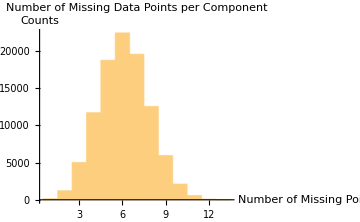

{Missing -> Counts: ,<|1→142,2→1220,3→5012,4→11693,5→18728,6→22396,7→19536,8→12532,9→5943,10→2117,11→573,12→96,13→12|>}

-Graphics-

<|186→<|10→{{-0.0440973},{15.}},15→{{0.0982086},{2.}},83→{{0.260952},{4.}},131→{{-0.0578792},{3.}},6366,88885→Missing[],91871→Missing[],92952→Missing[],96125→Missing[]|>,13,329→<|10→1,6372,1|>|>
 |  |  |  |

```mathematica
filteredProteinBootstrapData=FilterMissing[proteinBootstrapUnique,3/4]
```

For each bootstrap protein we now extract a time series (list of values):

```mathematica
timeSeriesProteinBootstrap=CreateTimeSeries[filteredProteinBootstrapData]
```

<|1|>
 |  |  |  |

Next, we normalize each protein series, using SeriesApplierpaclet:MathIOmica/ref/SeriesApplier:

```mathematica
normedProteinBootstrapAll=SeriesApplier[Normalize,timeSeriesProteinBootstrap]
```

<|10→{-0.031448,0.,0.0640716,-0.115008,0.0203035,-0.0586266,-0.0237844,20,-19,-0.0629589,-0.17116,Missing[],0.717319,Missing[],0.374911},6372,1|>
 |  |  |  |

Finally, we use ConstantSeriesCleanpaclet:MathIOmica/ref/ConstantSeriesClean to remove constant series, as we are interested in changing time patterns:

```mathematica
proteinBootstrapFinalTimeSeries=ConstantSeriesClean[normedProteinBootstrapAll]
```

<|10→{-0.031448,0.,0.0640716,-0.115008,0.0203035,-0.0586266,-0.0237844,20,-19,-0.0629589,-0.17116,Missing[],0.717319,Missing[],0.374911},6372,1|>
 |  |  |  |

### Classification of Proteome Time Series

In this subsection we will classify the proteome time series based on patterns in the series. For the classification we will use TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification. We will use QuantileEstimatorpaclet:MathIOmica/ref/QuantileEstimator for the "LombScargle" method to provide a cutoff for the TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification inputs.

First, we estimate for the "LombScargle" Method, 0.95 quantile cutoff from the bootstrap proteome data:

```mathematica
q95Protein=QuantileEstimator[proteinBootstrapFinalTimeSeries,timesProteinBootstrap]
```

0.835064

Next, we estimate the "Spikes" 0.95 quantile cutoff from the bootstrap proteome data:

```mathematica
q95ProteinSpikes=QuantileEstimator[proteinBootstrapFinalTimeSeries,timesProteinBootstrap,Method-> "Spikes"]
```

<|12→{0.804265,-0.838055},13→{0.802793,-0.81749},14→{0.787772,-0.821609}|>

Now we can classify the proteome time series data based on these cutoffs:

```mathematica
proteinClassification=TimeSeriesClassification[proteinFinalTimeSeries,timesProtein,LombScargleCutoff-> q95Protein,SpikeCutoffs->q95ProteinSpikes]
```

Method → "LombScargle"

<|1|>
 |  |  |  |

As discussed above, the default output for TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification is an Association with outer keys being the classification classes,  inner keys being the class members, and each class member value being a list of {{computed classification vector}, {input data list}}.

If we want the classes produced, we can query the keys:

```mathematica
Keys[proteinClassification]
```

{SpikeMax,SpikeMin,f1,f5,f6,f7}

For the number of members in each class we have:

```mathematica
Query[All,Length]@proteinClassification
```

<|SpikeMax→124,SpikeMin→48,f1→77,f5→7,f6→36,f7→18|>

We can obtain the membership list in any class of interest:

```mathematica
Query["f1",Keys]@proteinClassification
```

{{O00160,Protein},{O00267,Protein},{O00273,Protein},{O00571,Protein},{O15031,Protein},{O43143,Protein},{O43175,Protein},{O43312,Protein},{O43516,Protein},{O60271,Protein},{O60879,Protein},{O75643,Protein},{O75792,Protein},{O95498,Protein},{P00488,Protein},{P00915,Protein},{P02042,Protein},{P02671,Protein},{P04844,Protein},{P08174,Protein},{P09326,Protein},{P09496,Protein},{P11021,Protein},{P12956,Protein},{P13501,Protein},{P13611,Protein},{P13667,Protein},{P19387,Protein},{P23141,Protein},{P23368,Protein},{P32119,Protein},{P32189,Protein},{P33176,Protein},{P40306,Protein},{P42892,Protein},{P50225,Protein},{P51531,Protein},{P52888,Protein},{P54920,Protein},{P55036,Protein},{P60660,Protein},{P84095,Protein},{Q01518,Protein},{Q07021,Protein},{Q08722,Protein},{Q09666,Protein},{Q13151,Protein},{Q13217,Protein},{Q13488,Protein},{Q14165,Protein},{Q14643,Protein},{Q14653,Protein},{Q15084,Protein},{Q5H9R7,Protein},{Q6NYC8,Protein},{Q709C8,Protein},{Q86YP4,Protein},{Q92499,Protein},{Q96AT9,Protein},{Q96L92,Protein},{Q96RT1,Protein},{Q99439,Protein},{Q9BTE3,Protein},{Q9BTV4,Protein},{Q9BWS9,Protein},{Q9C0I1,Protein},{Q9H0D6,Protein},{Q9H2U2,Protein},{Q9H444,Protein},{Q9H4Z3,Protein},{Q9NS69,Protein},{Q9NUP9,Protein},{Q9NVJ2,Protein},{Q9NYB0,Protein},{Q9UQ35,Protein},{Q9Y277,Protein},{Q9Y2Q0,Protein}}

To obtain the possible frequencies we simply run LombScarglepaclet:MathIOmica/ref/LombScargle over the desired times for one of the time series and set the FrequenciesOnly option to Truepaclet:ref/True:

```mathematica
LombScargle[proteinFinalTimeSeries[[1]],timesRNA,FrequenciesOnly-> True]
```

<|f1→0.00500668,f2→0.0104306,f3→0.0158545,f4→0.0212784,f5→0.0267023,f6→0.0321262,f7→0.0375501|>

## Metabolomic Data

### Importing OmicsObject Metabolome Data

We now import the metabolomics data example (for details on how to import such data please refer to DataImporterpaclet:MathIOmica/ref/DataImporter, DataImporterDirectpaclet:MathIOmica/ref/DataImporterDirect, DataImporterDirectLabeledpaclet:MathIOmica/ref/DataImporterDirectLabeled and OmicsObjectCreatorpaclet:MathIOmica/ref/OmicsObjectCreator documentation).

We import the metabolomics OmicsObject MathIOmica examples for each of positive and negative mass spectrometry aligned mass features:

```mathematica
metabolitesNegativeModeExample=Get[FileNameJoin[{ConstantMathIOmicaExamplesDirectory,"metabolomicsNegativeModeExample"}]]
```

<|8→<|{457.002,0.34764,Meta}→{{23444,16317,1},{ [ C16 H11 N9 S4, db=0.00, overall=47.55, mfg=95.11 ],}},2289,{421.948,0.392875,Meta}→{{1,115528,130042},{ [ C11 H12 Cl2 O11 S, db=0.00, overall=48.58, mfg=97.17 ],}}|>,10,20→<|1|>|>
 |  |  |  |

```mathematica
metabolitesPositiveModeExample=Get[FileNameJoin[{ConstantMathIOmicaExamplesDirectory,"metabolomicsPositiveModeExample"}]]
```

<|8→<|{202.033,0.332607,Meta}→{{263741,276622,337241},{,}},{174.038,0.334514,Meta}→{{78435,88529,121073},{,}},3670,{422.34,14.7601,Meta}→{{1,36919,102737},{,}}|>,9→<|1|>,8,19→<|1|>,20→<|1|>|>
 |  |  |  |

There are multiple samples given by the outer associations. We can use Query to get any data. For example we can get the outer keys:

```mathematica
Query[Keys]@metabolitesNegativeModeExample
```

{8,9,10,11,12,13,14,15,16,17,19,20}

```mathematica
Query[Keys]@metabolitesPositiveModeExample
```

{8,9,10,11,12,13,14,15,16,17,19,20}

We notice that sample 7, 18 and 21 are missing as there was no sample for these time points. This will be addressed further below.

We can get the intensity data from any sample and entry. For example, the 77^th and 155^th entries in sample 14:

```mathematica
Query["14",{77,155}]@metabolitesNegativeModeExample
```

<|{322.089,0.440241,Meta}→{{31950,29801,27440},{Isosorbide-2-glucuronide [ C12 H18 O10, db=60.03, overall=60.67, mfg=61.31, KEGG ID=, CAS ID=29542-01-6 ],29542-01-6}},{146.059,0.742692,Meta}→{{62667,1,60382},{Adipic acid [ C6 H10 O4, db=45.74, overall=46.59, mfg=47.44, KEGG ID=, CAS ID=124-04-9 ],124-04-9}}|>

The outer keys correspond to the identified features in the form {mass to charge ratio (m/z), retention time, "Meta"}, i.e. each m/z and retention time has been tagged with a "Meta" label as well to indicate these are metabolomics data. The  values of all the keys/IDs correspond to {{measurements},{metadata}}, and in this particular example:  {{intensity technical replicate 1,intensity technical replicate 2,intensity technical replicate 3},{Annotations, CAS Number}}.

We would like to combine the positive and negative mode metabolomics data. We will use EnlargeInnerAssociationpaclet:MathIOmica/ref/EnlargeInnerAssociation:

```mathematica
metabolitesExample=EnlargeInnerAssociation[{metabolitesNegativeModeExample,metabolitesPositiveModeExample}]
```

<|8→<|{457.002,0.34764,Meta}→{{23444,16317,1},{ [ C16 H11 N9 S4, db=0.00, overall=47.55, mfg=95.11 ],}},5962,{422.34,14.7601,Meta}→{{1,36919,102737},{,}}|>,10,20→<|{457.002,0.34764,Meta}→{{1},1},5962,1|>|>
 |  |  |  |

### Processing of Metabolome Data

We will next preprocess the imported metabolome data. We will first perform calculate the median of the technical replicates, transform the data towards a normal distribution, then we will re-label the samples with real time and carry out filtering for missing data. Finally, we will create the metabolomics time series or relative intensities compared to the healthy reference point for each mass feature identified.

#### Medians of Technical Triplicates, Data Transformation, Labeling, Filtering, Matching Mass

##### Median of Technical Triplicates

The metabolomics intensities have three measurements, corresponding to technical triplicates. Typically we would like to use the median of these values. An additional complication is that some of the triplicates have intensity values of 1, which should be taken as a Missing value. We can use MeasurementApplier to perform the calculation:

MeasurementApplier[function,omicsObject] | applies a function to the measurement list of an omicsObject, ignoring missing values.

Applying a function to the measurements in an OmicsObject.

option name | default value |  
ComponentIndex | All | ComponentIndexpaclet:MathIOmica/ref/ComponentIndex is an option for MathIOmica functions, such as Applierpaclet:MathIOmica/ref/Applier, that allows selection of which component of a list to use in an association or OmicsObject input or output values.
IgnorePattern | _Missing | IgnorePattern is an option for MeasurementApplier specifying a pattern of values to delete prior to applying the function to the measurement list.
ListIndex | 1 | ListIndexpaclet:MathIOmica/ref/ListIndex is an option for MathIOmica functions, such as Applierpaclet:MathIOmica/ref/Applier that allows selection of which list to use in the association or OmicsObject input or output values.

Options for MeasurementApplierpaclet:MathIOmica/ref/MeasurementApplier.

We implement a Median calculation, and ignoring entries with missing and values of 1:

```mathematica
metaboliteMedians=MeasurementApplier[Median,metabolitesExample,IgnorePattern->(_Missing| 1|1.)]
```

<|8→<|{457.002,0.34764,Meta}→{{19880.5},{ [ C16 H11 N9 S4, db=0.00, overall=47.55, mfg=95.11 ],}},5962,{422.34,14.7601,Meta}→{{69828.},{,}}|>,10,20→<|{457.002,0.34764,Meta}→{{16606.5},{1}},5962,{1}→1|>|>
 |  |  |  |

##### Data Power Transformation

We apply a Box-Cox transformation to the metabolite median data in the OmicsObject, which is now the first list first component for each identifier. The optimized λ̂ parameter for each sample is printed out for reference:

```mathematica
transformedMetaboliteData=ApplyBoxCoxTransform[metaboliteMedians,ListIndex-> 1,ComponentIndex-> 1]
```

Calculated Box-Cox parameter λ̂ = -0.288857

Calculated Box-Cox parameter λ̂ = -0.282374

Calculated Box-Cox parameter λ̂ = -0.276202

Calculated Box-Cox parameter λ̂ = -0.262075

Calculated Box-Cox parameter λ̂ = -0.271308

Calculated Box-Cox parameter λ̂ = -0.27703

Calculated Box-Cox parameter λ̂ = -0.295395

Calculated Box-Cox parameter λ̂ = -0.264833

Calculated Box-Cox parameter λ̂ = -0.278556

Calculated Box-Cox parameter λ̂ = -0.269513

Calculated Box-Cox parameter λ̂ = -0.265784

Calculated Box-Cox parameter λ̂ = -0.262769

<|8→<|{457.002,0.34764,Meta}→{{3.26345},{ [ C16 H11 N9 S4, db=0.00, overall=47.55, mfg=95.11 ],}},5962,{422.34,14.7601,Meta}→{{3.32386},{,}}|>,10,20→<|{457.002,0.34764,Meta}→{1},5962,1|>|>
 |  |  |  |

We can plot the data to see what the resulting distributions look like:

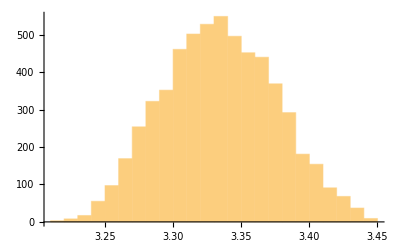
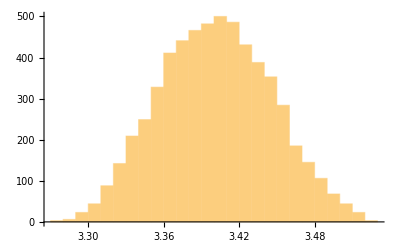
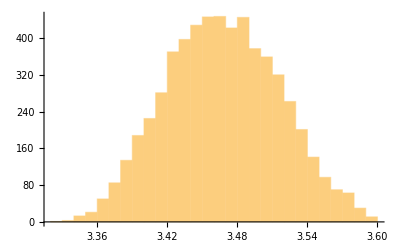
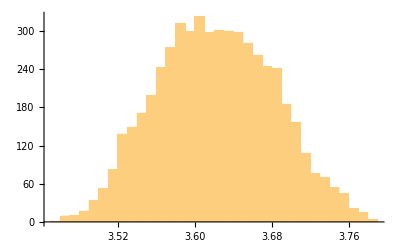
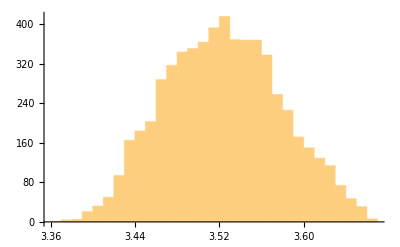
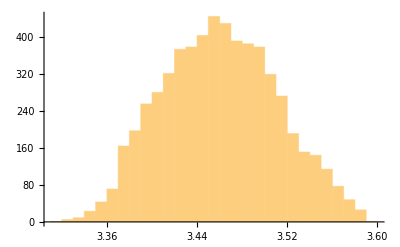
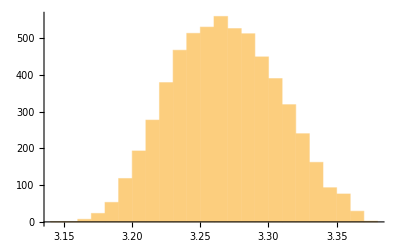
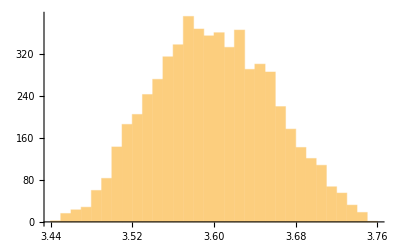
<|8→-Graphics-,9→-Graphics-,10→-Graphics-,11→-Graphics-,12→-Graphics-,13→-Graphics-,14→-Graphics-,15→-Graphics-,16→-Graphics-,17→-Graphics-,19→-Graphics-,20→-Graphics-|>

```mathematica
Histogram[#]&/@(Query[All,Values,1,1]@transformedMetaboliteData)
```

We may also wish to standardize the distributions:

```mathematica
metabolitesStandardized=Returner[transformedMetaboliteData,Applier[StandardizeExtended[#,Mean,StandardDeviation]&,transformedMetaboliteData,ListIndex-> 1,ComponentIndex-> 1],ListIndex-> 1,ComponentIndex-> 1]
```

<|8→<|{457.002,0.34764,Meta}→{{-1.71178},{ [ C16 H11 N9 S4, db=0.00, overall=47.55, mfg=95.11 ],}},5962,{422.34,14.7601,Meta}→{{-0.247328},{,}}|>,10,20→<|{457.002,0.34764,Meta}→{1},5962,1|>|>
 |  |  |  |

We can again plot the data to see what the standardized distributions look like:

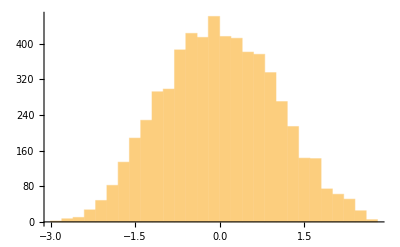
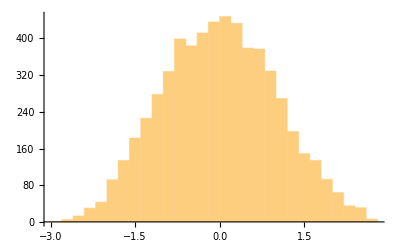
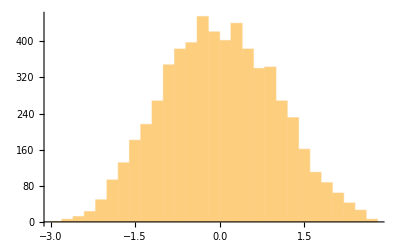
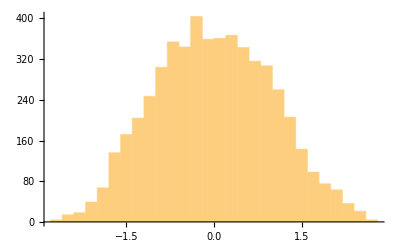
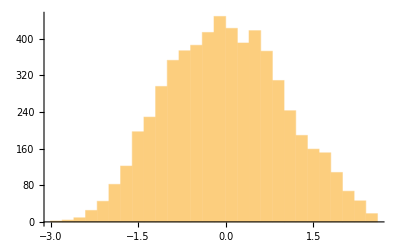
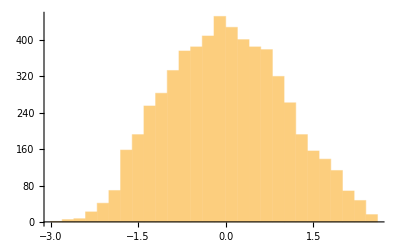
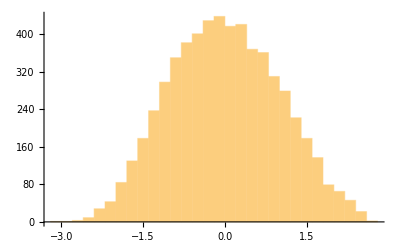
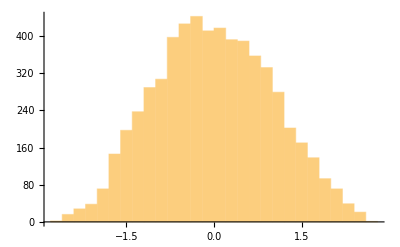
<|8→-Graphics-,9→-Graphics-,10→-Graphics-,11→-Graphics-,12→-Graphics-,13→-Graphics-,14→-Graphics-,15→-Graphics-,16→-Graphics-,17→-Graphics-,19→-Graphics-,20→-Graphics-|>

```mathematica
Histogram[#]&/@(Query[All,Values,1,1]@metabolitesStandardized)
```

##### Re-labeling Samples with Times

As with the transcriptome, we notice that the sample numberings do not correspond to actual days, so we may adjust using the sampleToDays association created above:

```mathematica
sampleToDays= <|"7"->"186","8"->"255","9"->"289","10"->"290","11"->"292","12"->"294","13"->"297","14"->"301","15"->"307","16"->"311","17"->"322","18"->"329","19"->"369","20"->"380","21"->"400"|>;
```

We can now do a KeyMap to rename the outer keys:

```mathematica
metabolitesLongitudinal=KeyMap[sampleToDays,metabolitesStandardized]
```

<|255→<|{457.002,0.34764,Meta}→{{-1.71178},{ [ C16 H11 N9 S4, db=0.00, overall=47.55, mfg=95.11 ],}},5962,{422.34,14.7601,Meta}→{{-0.247328},{,}}|>,10,380→<|{457.002,0.34764,Meta}→{1},5963|>|>
 |  |  |  |

Now let's check the timepoints in this dataset:

```mathematica
timesMetaboliteRawData=TimeExtractor[metabolitesLongitudinal]
```

{255,289,290,292,294,297,301,307,311,322,369,380}

We notice a complication: there are three timepoints missing, corresponding to the three samples for which we had indicated above that there were no measurements (compared to the transcriptome samples). These are samples on days "186", "329" and "400".

We can use the ConstantAssociatorpaclet:MathIOmica/ref/ConstantAssociator function to append these to the transformed data, tagging these data as Missing data:

```mathematica
metabolitesLongitudinalEnlarged=ConstantAssociator[metabolitesLongitudinal,<|"186"-> Missing[],"329"-> Missing[],"400"-> Missing[]|>]
```

<|255→<|{457.002,0.34764,Meta}→{{-1.71178},{ [ C16 H11 N9 S4, db=0.00, overall=47.55, mfg=95.11 ],}},5962,{422.34,14.7601,Meta}→{{-0.247328},{,}}|>,13,400→<|{457.002,0.34764,Meta}→1,5962,1|>|>
 |  |  |  |

We can now check the timepoints again:

```mathematica
timesMetabolites=TimeExtractor[metabolitesLongitudinalEnlarged]
```

{186,255,289,290,292,294,297,301,307,311,322,329,369,380,400}

##### Filter Data

We will next remove values that have been tagged overall as Missing[], retaining data that have at least 3/4 data points available across all samples. Additionally we remove data where the reference healthy sample "255" was missing. We use the function FilterMissingpaclet:MathIOmica/ref/FilterMissing for this implementation:

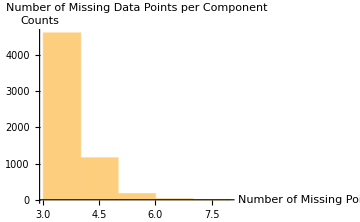

{Missing -> Counts: ,<|3→4601,4→1158,5→172,6→31,7→2|>}

-Graphics-

<|255→<|{457.002,0.34764,Meta}→{{-1.71178},{ [ C16 H11 N9 S4, db=0.00, overall=47.55, mfg=95.11 ],}},4599,{406.381,14.5609,Meta}→{{-1.34842},{2,4,6-trimethyl-2,15…ipid ID=, KEGG ID= ],}}|>,13,400→<|1|>|>
 |  |  |  |

```mathematica
filteredMetaboliteData=FilterMissing[metabolitesLongitudinalEnlarged,3/4,Reference-> "255"]
```

##### Matching Unique Mass

We may want to match a unique mass to the metabolites. This is a putative mass identification based on the uniqueness of the mass feature. If matched, a KEGG compound identity can be prepended to the identifier using OmicsObjectUniqueMassConverterpaclet:MathIOmica/ref/OmicsObjectUniqueMassConverter.

OmicsObjectUniqueMassConverter[omicsObject, massAccuracy] | assigns a unique putative mass identification to each of omicsObject's inner association keys, using the massAccuracy in parts per million.

Matching putative mass identifications to mass features in an OmicsObjectpaclet:MathIOmica/ref/OmicsObject of metabolites.

We match our identities to KEGG compound identifiers, using a 2ppm accuracy (this may take some time depending on the number of matching data):

```mathematica
massMatchedFilteredMetabolites=OmicsObjectUniqueMassConverter[filteredMetaboliteData,2]
```

<|255→<|{457.002,0.34764,Meta}→{{-1.71178},{ [ C16 H11 N9 S4, db=0.00, overall=47.55, mfg=95.11 ],}},4599,{406.381,14.5609,Meta}→{{-1.34842},{2,4,6-trimethyl-2,…id ID=, KEGG ID= ],}}|>,13,400→<|1|>|>
 |  |  |  |

#### Create Metabolome Time Series

We can now create time series for each of the proteins.

For each metabolite feature we now extract a time series (list of values) corresponding to the set of times:

```mathematica
timeSeriesMetabolites=CreateTimeSeries[massMatchedFilteredMetabolites]
```

<|1|>
 |  |  |  |

#### Take Difference Compared to Reference in Metabolome Time Series.

Now we need to compare  to compare the difference of each intensity for a given metabolite's time series to the intensity of the ratios of expression at any time point compared to a healthy datapoint. We can use the function SeriesInternalComparepaclet:MathIOmica/ref/SeriesInternalCompare:

We compare every value in each series to the healthy "255" time point, which is the second element in each series:

```mathematica
metabolitesCompared=SeriesInternalCompare[timeSeriesMetabolites,ComparisonIndex->2]
```

<|{457.002,0.34764,Meta}→{Missing[],0.,-0.326659,-0.244843,0.0307746,-0.112847,3,-0.640794,-0.165613,Missing[],-0.340455,-0.143904,Missing[]},4599,{1}→1|>
 |  |  |  |

#### Take the Norm and Remove Constant Metabolome Time Series

Next, we normalize each series, using again SeriesApplierpaclet:MathIOmica/ref/SeriesApplier:

```mathematica
normedMetabolitesCompared=SeriesApplier[Normalize,metabolitesCompared]
```

<|{457.002,0.34764,Meta}→{Missing[],0.,-0.343784,-0.25768,0.032388,-0.118763,3,-0.674389,-0.174295,Missing[],-0.358304,-0.151448,Missing[]},4600|>
 |  |  |  |

Finally, we use ConstantSeriesCleanpaclet:MathIOmica/ref/ConstantSeriesClean to remove constant series, as we are interested in changing time patterns:

```mathematica
metabolomeFinalTimeSeries=ConstantSeriesClean[normedMetabolitesCompared]
```

<|{457.002,0.34764,Meta}→{Missing[],0.,-0.343784,-0.25768,0.032388,-0.118763,3,-0.674389,-0.174295,Missing[],-0.358304,-0.151448,Missing[]},4600|>
 |  |  |  |

### Resampling Metabolome Data

We also would like to create a resampled distribution for the metabolome dataset prior to classification and clustering. In this subsection we first resample the imported metabolome dataset. Then, we carry out the full analysis in this "bootstrap" dataset, to create a set of random metabolome time series. This bootstrap distribution of time series will be used to provide the cutoffs used in the time series classification in the following subsection.

#### Resampling the Proteome Data

We create a resampling of 100000 sets:

```mathematica
metabolitesBootstrap=BootstrapGeneral[metabolitesExample,100000]
```

<|8→<|1→{{88478,100725,59680},{2-pentadecenoic acid [ C15 H28 O2, db=82.32, overall=82.52, mfg=46.15, Lipid ID=, KEGG ID= ],}},99998,100000→{{44327,153862,33442},{5alpha-Cholan-24-oic Acid….87, Lipid ID=, KEGG ID= ],}}|>,10,20→<|1|>|>
 |  |  |  |

#### Processing the Bootstrap Metabolome and Creating Bootstrap Time Series

We implement a Median calculation, and ignoring entries with missing and values of 1 for the bootstrap set:

```mathematica
metaboliteBootstrapMedians=MeasurementApplier[Median,metabolitesBootstrap,IgnorePattern->(_Missing| 1|1.)];
```

We apply a Box-Cox transformation to the bootstrap metabolite median data in the OmicsObject, which is now the first list first component for each identifier. The optimized λ̂ parameter for each sample is printed out for reference:

```mathematica
transformedBootstrapMetaboliteData=ApplyBoxCoxTransform[metaboliteBootstrapMedians,ListIndex-> 1,ComponentIndex-> 1]
```

Calculated Box-Cox parameter λ̂ = -0.287152

Calculated Box-Cox parameter λ̂ = -0.280376

Calculated Box-Cox parameter λ̂ = -0.276347

Calculated Box-Cox parameter λ̂ = -0.260243

Calculated Box-Cox parameter λ̂ = -0.270257

Calculated Box-Cox parameter λ̂ = -0.273974

Calculated Box-Cox parameter λ̂ = -0.294708

Calculated Box-Cox parameter λ̂ = -0.265066

Calculated Box-Cox parameter λ̂ = -0.280128

Calculated Box-Cox parameter λ̂ = -0.269042

Calculated Box-Cox parameter λ̂ = -0.265108

Calculated Box-Cox parameter λ̂ = -0.262923

<|8→<|1→{{3.35022},{2-pentadecenoic acid [ C15 H28 O2, db=82.32, overall=82.52, mfg=46.15, Lipid ID=, KEGG ID= ],}},2→{1},99996,99999→1,100000→{{3.32119},{5alpha-Cholan-24-oic Acid [ …96.87, Lipid ID=, KEGG ID= ],}}|>,10,1|>
 |  |  |  |

We may also wish to standardize the distributions:

```mathematica
metabolitesBootstrapStandardized=Returner[transformedBootstrapMetaboliteData,Applier[StandardizeExtended[#,Mean,StandardDeviation]&,transformedBootstrapMetaboliteData,ListIndex-> 1,ComponentIndex-> 1],ListIndex-> 1,ComponentIndex-> 1]
```

<|8→<|1→{{-0.0237496},{2-pentadecenoic acid [ C15 H28 O2, db=82.32, overall=82.52, mfg=46.15, Lipid ID=, KEGG ID= ],}},2→{1},99996,99999→1,100000→{{-0.714262},{5alpha-Cholan-24-oic Acid ….87, Lipid ID=, KEGG ID= ],}}|>,10,1|>
 |  |  |  |

We can now do a KeyMap to rename the outer keys with labels corresponding to days:

```mathematica
metabolitesBootstrapLongitudinal=KeyMap[sampleToDays,metabolitesBootstrapStandardized];
```

Now let's check the timepoints in this dataset:

```mathematica
timesMetaboliteBootstrapData=TimeExtractor[metabolitesBootstrapLongitudinal]
```

{255,289,290,292,294,297,301,307,311,322,369,380}

We can use the ConstantAssociatorpaclet:MathIOmica/ref/ConstantAssociator function to append the "186", "329" and "400" missing days to the transformed bootstrap data:

```mathematica
metabolitesBootstrapLongitudinalEnlarged=ConstantAssociator[metabolitesBootstrapLongitudinal,<|"186"-> Missing[],"329"-> Missing[],"400"-> Missing[]|>];
```

We can now check the timepoints again:

```mathematica
timesMetabolitesBootstrap=TimeExtractor[metabolitesBootstrapLongitudinalEnlarged]
```

{186,255,289,290,292,294,297,301,307,311,322,329,369,380,400}

We next remove values that have been tagged overall as Missing[], retaining data that have at least 3/4 data points available across all samples. Additionally we remove data where the reference healthy sample "255" was missing. We use the function FilterMissingpaclet:MathIOmica/ref/FilterMissing for this implementation:

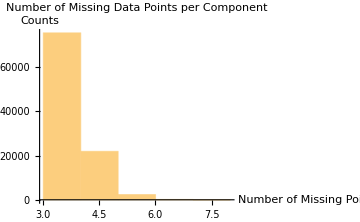

{Missing -> Counts: ,<|3→75579,4→21924,5→2352,6→142,7→3|>}

-Graphics-

```mathematica
filteredMetaboliteBootstrapData=FilterMissing[metabolitesBootstrapLongitudinalEnlarged,3/4,Reference-> "255"];
```

For each bootstrap metabolite feature we now extract a time series (list of values) corresponding to the set of times:

```mathematica
timeSeriesMetabolitesBootstrap=CreateTimeSeries[filteredMetaboliteBootstrapData];
```

We compare every value in each bootstrap series to the healthy "255" time point, which is the second element in each series:

```mathematica
metabolitesBootstrapCompared=SeriesInternalCompare[timeSeriesMetabolitesBootstrap,ComparisonIndex->2];
```

Next, we normalize each series, using again SeriesApplierpaclet:MathIOmica/ref/SeriesApplier:

```mathematica
normedMetabolitesBootstrapCompared=SeriesApplier[Normalize,metabolitesBootstrapCompared];
```

Finally, we use ConstantSeriesCleanpaclet:MathIOmica/ref/ConstantSeriesClean to remove constant series, as we are interested in changing time patterns:

```mathematica
metabolomeBootstrapFinalTimeSeries=ConstantSeriesClean[normedMetabolitesBootstrapCompared];
```

### Classification of Metabolome Time Series

In this subsection we will classify the metabolome time series based on patterns in the series. For the classification we will use TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification. We will use QuantileEstimatorpaclet:MathIOmica/ref/QuantileEstimator for the "LombScargle" method to provide a cutoff for the TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification inputs.

First, we estimate for the "LombScargle" Method, 0.95 quantile cutoff from the bootstrap metabolome data:

```mathematica
q95Metabolites=QuantileEstimator[metabolomeBootstrapFinalTimeSeries,timesMetabolitesBootstrap]
```

0.846125

Next, we estimate the "Spikes" 0.95 quantile cutoff from the bootstrap proteome data:

```mathematica
q95MetabolitesSpikes=QuantileEstimator[metabolomeBootstrapFinalTimeSeries,timesMetabolitesBootstrap,Method-> "Spikes"]
```

<|12→{0.67052,-0.651833}|>

Now we can classify the proteome time series data based on these cutoffs:

```mathematica
metaboliteClassification=TimeSeriesClassification[metabolomeFinalTimeSeries,timesMetabolites,LombScargleCutoff-> q95Metabolites,SpikeCutoffs->q95MetabolitesSpikes]
```

Method → "LombScargle"

<|SpikeMax→<|{1514.1,0.366235,Meta}→{{0.150094,0.150759,0.336515,0.197558,0.430385,0.667846,0.41379},{Missing[],0.,12,Missing[]}},134,{1}→1|>,6|>
 |  |  |  |

As discussed above, the default output for TimeSeriesClassification is an Association with outer keys being the classification classes,  inner keys being the class members, and each class member value being a list of {{computed classification vector}, {input data list}}.

If we want the classes produced, we can query the keys:

```mathematica
Keys[metaboliteClassification]
```

{SpikeMax,SpikeMin,f1,f2,f5,f6,f7}

For the number of members in each class we have:

```mathematica
Query[All,Length]@metaboliteClassification
```

<|SpikeMax→136,SpikeMin→713,f1→63,f2→38,f5→43,f6→15,f7→33|>

We can obtain the membership list in any class of interest:

```mathematica
Query["f1",Keys]@metaboliteClassification
```

{{373.859,0.411324,Meta},{cpd:C11821,184.024,0.653444,Meta},{221.109,10.3062,Meta},{cpd:C18218,272.235,12.7737,Meta},{294.166,13.0495,Meta},{631.385,13.5221,Meta},{563.32,13.7008,Meta},{779.604,13.9622,Meta},{362.266,14.001,Meta},{cpd:C17873,384.36,14.2982,Meta},{390.297,14.3592,Meta},{420.361,14.6658,Meta},{434.376,14.7796,Meta},{392.366,15.0173,Meta},{394.381,15.1519,Meta},{1599.15,15.281,Meta},{693.628,15.6921,Meta},{874.715,15.9118,Meta},{281.986,0.390455,Meta},{504.309,14.3911,Meta},{416.313,14.4627,Meta},{735.521,15.1792,Meta},{571.961,0.388167,Meta},{489.958,0.388912,Meta},{325.95,0.392472,Meta},{465.913,0.393056,Meta},{383.909,0.397722,Meta},{301.906,0.407861,Meta},{219.903,0.412111,Meta},{161.944,0.413086,Meta},{139.061,0.458472,Meta},{115.064,0.463972,Meta},{71.074,0.482559,Meta},{253.165,9.12729,Meta},{298.132,9.30967,Meta},{cpd:C20605,411.179,9.3167,Meta},{440.201,11.2909,Meta},{355.218,12.7443,Meta},{338.244,12.8545,Meta},{1061.15,13.0612,Meta},{210.198,13.1613,Meta},{501.367,13.296,Meta},{594.375,13.3701,Meta},{1538.03,13.3796,Meta},{404.314,13.6028,Meta},{692.323,13.7652,Meta},{670.265,13.8732,Meta},{814.584,14.1513,Meta},{366.349,14.3015,Meta},{442.402,14.3568,Meta},{406.381,14.3581,Meta},{278.152,14.364,Meta},{cpd:C19658,344.271,14.4331,Meta},{420.358,14.4446,Meta},{311.319,14.6119,Meta},{791.583,15.4236,Meta},{1553.18,15.4429,Meta},{1545.17,15.5017,Meta},{352.052,0.53368,Meta},{cpd:C17237,254.073,12.2926,Meta},{336.228,12.5103,Meta},{638.402,13.4139,Meta},{668.324,13.988,Meta}}

To obtain the possible frequencies we simply run LombScarglepaclet:MathIOmica/ref/LombScargle over the desired times for one of the time series and set the FrequenciesOnly option to Truepaclet:ref/True:

```mathematica
LombScargle[metabolomeFinalTimeSeries[[1]],timesMetabolites,FrequenciesOnly-> True]
```

<|f1→0.00500668,f2→0.0104306,f3→0.0158545,f4→0.0212784,f5→0.0267023,f6→0.0321262,f7→0.0375501|>

## Combined Data Clustering

In this section we will combine the omics data classes from the individual classifications above using JoinNestedAssociationspaclet:MathIOmica/ref/JoinNestedAssociations  and hierarchically cluster the information to obtain a second level of classification using TimeSeriesClusterspaclet:MathIOmica/ref/TimeSeriesClusters. We will visualize the results in the following section.

### Combining Multi-omics Classified Data

JoinNestedAssociations[associationList] | merges the nested associationList (an association of associations) by joining the inner associations for each matching key.

Joining classification data.

We combine the classification data using JoinNestedAssociationspaclet:MathIOmica/ref/JoinNestedAssociations:

```mathematica
combinedClassification=JoinNestedAssociations[{rnaClassification,proteinClassification,metaboliteClassification }]
```

<|SpikeMax→<|{ATAD3C,RNA}→{{0.0855374,0.204135,0.219303,0.378496,0.5849,0.346012,0.545735},{0.,0.,0.,0.,7,0.,0.,0.075919,0.}},1081|>,7,f7→<|1|>|>
 |  |  |  |

We can check the keys before and after the combination:

```mathematica
Keys[#]&/@{rnaClassification,proteinClassification,metaboliteClassification }
```

{{SpikeMax,SpikeMin,f1,f2,f3,f4,f5,f6,f7},{SpikeMax,SpikeMin,f1,f5,f6,f7},{SpikeMax,SpikeMin,f1,f2,f5,f6,f7}}

```mathematica
Keys@combinedClassification
```

{SpikeMax,SpikeMin,f1,f2,f3,f4,f5,f6,f7}

We can also check the membership counts before and after the combination:

```mathematica
Query[All,Length]@#&/@{rnaClassification,proteinClassification,metaboliteClassification }
```

{<|SpikeMax→822,SpikeMin→5963,f1→116,f2→3,f3→30,f4→128,f5→35,f6→13,f7→61|>,<|SpikeMax→124,SpikeMin→48,f1→77,f5→7,f6→36,f7→18|>,<|SpikeMax→136,SpikeMin→713,f1→63,f2→38,f5→43,f6→15,f7→33|>}

```mathematica
Query[All,Length]@combinedClassification
```

<|SpikeMax→1082,SpikeMin→6724,f1→256,f2→41,f3→30,f4→128,f5→85,f6→64,f7→112|>

### Clustering of Classified Data

Now that we have combined the classes for the various omics, we can cluster them together to obtain the various trends using TimeSeriesClusterspaclet:MathIOmica/ref/TimeSeriesClusters. A two-tier hierarchical clustering of the data is performed, using a set of two classification vectors, {{classification vector_1}, {classification vector_2}} for each time series to cluster the data pairwise. The vectors are typically the output from TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification. Similarities at each clustering tier are then computed using in succession from each time series first {classification vector_1}, and subsequently {classification vector_2} (which corresponds to the {input data time series} if the input is from TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification).

The number of groups and subgroups for each tier of clustering is automatically determined by using internally the "Silhouette" (default) or "Gap" as "SignificanceTest" methods (see also Partitioning Data into Clusters).

TimeSeriesClusters[data] | performs clustering of time series data using two tiers of hierarchical clustering to identify groups and subgroups in the data. TimeSeriesClusters takes as input series data, where each data is comprised of two lists and performs clustering of the data to identify groups and subgroups based on similarities between the input series. The form of the input data is either an association of classes and members, where each member must have a list of two components, typically two vectors used in classification: {{classification vector_1}, {classification vector_2}}.
In the most common case of using as input data that came from performing a TimeSeriesClassification, the {classification vector_2} will correspond to input original data for the corresponding time series.

Clustering of classified time series.

option name | default value |  
ClusterLabeling | "" | Additional label to append to each cluster being computed to prepend to the inbuilt G#S# labeling.
DendrogramPlotOptions | {} | Options passed to the DendrogramPlot function used internally to generate the dendrograms.
DistanceFunction | EuclideanDistance | Distance function to be used in calculating the similarities between different time series in the first tier of clustering.
LinkageMeasure | "Average" | Which linkage measure to use in computing fusion coefficients.
PrintDendrograms | False | Option to print dendrograms for the clustering computed.
ReturnDendrograms | False | Option to return the dendrograms as output.
SignificanceCriterion | "Silhouette" | Method used in determining the number of groups and subgroups at each tier of clustering.
SingleAssociationLabel | "1" | Label to use in case a list is provided to name the class of data produced.
SubclusteringDistanceFunction | EuclideanDistance | Distance function to be used in calculating the similarities between different time series in the second tier of clustering.

Options for TimeSeriesClusterspaclet:MathIOmica/ref/TimeSeriesClusters.

The output of TimeSeriesClusters is always an association of associations, providing a summary of the two tier clustering results for each class provided in the input. The output has the form:

output= 
<| Class_1 →  <|"Cluster"→ cluster object_1,
"InitialSplitCluster"→  {InitialSplitCluster_11,InitialSplitCluster_12...}, 
"IntermediateClusters"→  {IntermediateCluster_11,IntermediateCluster_12...},
"SubsplitClusters"→  {{SubsplitClusters_11}{SubsplitClusters_12}},
"Data"→  {{input data vector_11}→ Member_11,...,},
"GroupAssociations"→  <|"G1S1"→{member list G1S1},
 "G1S2"→ {member list for G1S2},
...,
"G2S1"→{...}|>|>,
Class_2 →  <|"Cluster"→ cluster object_2,
"InitialSplitCluster"→  {InitialSplitCluster_21,InitialSplitCluster_22...},
"IntermediateClusters"→  {IntermediateCluster_21,IntermediateCluster_22...},
"SubsplitClusters"→  {{SubsplitClusters_21}{SubsplitClusters_22}},
"Data"→  {{input data vector_21}→ Member_21,...,},
"GroupAssociations"→  <|"G1S1"→{member list G1S1},
 "G1S2"→ {member list for G1S2},
...,
"G2S1"→{...}|>|>,
...,
Class_M →  <|"Cluster"→ cluster object_M,
"InitialSplitCluster"→  {InitialSplitCluster_M1,InitialSplitCluster_M2...},
"IntermediateClusters"→  {IntermediateCluster_M1,IntermediateCluster_M2...},
"SubsplitClusters"→  {{subsplitClusters_M1}{subsplitClusters_M2}},
"Data"→  {{input data vector_M1}→ Member_M1,...,},
"GroupAssociations"→  <|"G1S1"→{member list G1S1},
 "G1S2"→ {member list for G1S2},
...,
"G2S1"→{...}|>|>
|>

Method | Description
"Cluster" | Cluster generated using the input {classification vector_1} for similarity calculations. 
"InitialSplitCluster" | Clusters resulting from splitting the initial cluster (reported by key "Cluster") into groups using the SignificanceCriterion to determine the number of clusters.
"IntermediateClusters" | Aglomerative clustering result of hierarchical clustering of each of the initial split clusters (reported by "InitialSplitCluster")
"SubsplitClusters" | Custers generated from splitting the clusters following the second tier clustering (reported by "IntermediateClusters") into subgroups using the SignificanceCriterion to determine the number of clusters.
"Data" | Data reported in the order of clustering results as rules of {classification vector_2}→ label for each time series, sorted in order of the clustering results.
"GroupAssociations" | Association denoting membership of each initial data label to groups and subgroups generated by the two tier clustering.

Output keys for TimeSeriesClusterspaclet:MathIOmica/ref/TimeSeriesClusters provide clustering information.

We now cluster our combined data (a printout of the clusters is included as a default option):

```mathematica
combinedClusters=TimeSeriesClusters[combinedClassification]
```

<|SpikeMax→<|1|>,SpikeMin→<|1|>,5,f6→1,f7→<|Cluster→Cluster[1],4,GroupAssociations→<|G1S1→{{MIR6723,RNA},{ZNF324,RNA},{CBX6,RNA},106,{O60884,Protein},{RTFDC1,RNA},{246.121,0.940379,Meta}}|>|>|>
 |  |  |  |

## Visualization

After our data have been clustered, we would like to visualise the results in heatmaps and dendrograms. For the two-tier clustering we have performed MathIOmica can output all the clusterings in labeled dendrograms and heatmaps using TimeSeriesDendrogramsHeatmapspaclet:MathIOmica/ref/TimeSeriesDendrogramsHeatmaps, which iteratively calls TimeSeriesDendrogramHeatmappaclet:MathIOmica/ref/TimeSeriesDendrogramHeatmap on each class.

TimeSeriesDendrogramsHeatmaps[data] | generates  dendrograms and associated heatmap plots for clustered time series data, typically the output of all classes generated by implementing  TimeSeriesClusterspaclet:MathIOmica/ref/TimeSeriesClusters. 
TimeSeriesDendrogramHeatmap[data] | generates a dendrogram and heatmap plot for one set of time series data clusters, typically the output of a single class of  TimeSeriesClusterspaclet:MathIOmica/ref/TimeSeriesClusters.

Visualizing the results of classification.

option name | default value |  
FunctionOptions | {ImageSize -> 200} | Options list passed to the internal TimeSeriesDendrogramHeatmappaclet:MathIOmica/ref/TimeSeriesDendrogramHeatmap function.

Options for TimeSeriesDendrogramsHeatmapspaclet:MathIOmica/ref/TimeSeriesDendrogramsHeatmaps.

option name | default value |  
ColorBlending | {CMYKColor[1, 0, 1, 0], CMYKColor[0, 1, 1, 0]} | Color scheme for the plot. The color list is passed to an internal Blend function to create a ColorFunction for an internal ArrayPlot function.
DendrogramColor | RGBColor[1, 1, 0] | Color to highlight the dendrograms.
FrameName | "Dendrogram and Heatmap" | Label for plot frame.
GroupSubSize | {0.1, 0.1} | Relative size of group and subgroup reference column in plot.
HorizontalAxisName | "Time (arbitrary units)" | Label for the horizontal heatmap axis.
HorizontalLabels | None | Labels for horizontal axis for each column.
IndexColor | "DeepSeaColors" | Choice of color for labeling the group/subgroup index.
ImageSize | 200 | ImageSize is an option that specifies the overall size of an image to display for an object. 
ScaleShift | None | Option to reset the blend of the colors used overall. The option is a real positive number, and is used as a multiplier for an internal Blend function's second argument.
VerticalLabels | None | Labels for vertical axis for each row.

Options for TimeSeriesDendrogramHeatmappaclet:MathIOmica/ref/TimeSeriesDendrogramHeatmap.

For each class a separate plot is generated: dendrograms are represented on the left, and are highlighted to represent the grouping level. The G, S, columns represent the groupings and subgroupings generated by the clustering.  The legend shows the corresponding groupings and subgrouping, and the number of elements in each group subgroup.

```mathematica
TimeSeriesDendrogramsHeatmaps[combinedClusters]
```

-Graphics-

## Annotation and Enrichment

Having carried out the classification and clustering of data base on its temporal pattern, we would like to perform annotation of these data for gene ontology (GO) and pathways from KEGG: Kyoto Encyclopedia of Genes and Genomes.

### Gene Ontology Analysis

MathIOmica provides a GOAnalysispaclet:MathIOmica/ref/GOAnalysis function using annotations (default is for human data) obtained from the Gene Ontology consortium, and by default uses human data annotated with UniProt IDs. The GOAnalysispaclet:MathIOmica/ref/GOAnalysis function performs an over-representation (ORA) analysis, providing a "significance" cutoff based on a p-value assessed by a hypergeometric function.

GOAnalysis[data] | calculates input data over-representation analysis (ORA) for Gene Ontology (GO) categories. We note that the function utilizes ontologies obtained from the GO Consortium, and by default uses human data annotated with UniProt IDs.

Performing an over representation analysis for Gene Ontology (GO) terms, using clustered data in MathIOmica.

option name | default value |  
AdditionalFilter | None | AdditionalFilter provides additional filtering that may be applied to the standard output structure to be returned. 
AugmentDictionary | True | AugmentDictionary provides a choice whether or not to augment the current ConstantGeneDictionarypaclet:MathIOmica/ref/ConstantGeneDictionary variable or create a new one.
BackgroundSet | All | BackgroundSet provides a list of IDs (e.g. gene accessions) that should be considered as the background for the calculation.
FilterSignificant | True | FilterSignificant can be set to True to filter data based on whether the enrichment analysis is statistically significant, or if set to False to return all membership computations.
GeneDictionary | None | GeneDictionary points to an existing variable to use as a gene dictionary in annotations. If set to None the default ConstantGeneDictionarypaclet:MathIOmica/ref/ConstantGeneDictionary will be used.
GetGeneDictionaryOptions | {} | The GetGeneDictionaryOptions option specifies a list of options that will be passed to the internal GetGeneDictionarypaclet:MathIOmica/ref/GetGeneDictionary function.
GOAnalysisAssignerOptions | {} | The GOAnalysisAssignerOptions option specifies a list of options that will be passed to the internal GOAnalysisAssignerpaclet:MathIOmica/ref/GOAnalysisAssigner function.
HypothesisFunction | (Query["Results"][BenjaminiHochbergFDR[#1, SignificanceLevel -> #2]] &)  | The HypothesisFunction option allows us to chose a function to implement multiple hypothesis testing.  The default is  using the BenjaminiHochbergFDRpaclet:MathIOmica/ref/BenjaminiHochbergFDR function.
The user can use any function f with three inputs, of the form f[#1,#2,#3] where the inputs refer to:
#1 is the p-value list, 
#2 is a significance cutoff, 
#3 is the number of GO associations overall being tested. 
The function f must output a list of 3 values: {original p-value, adjusted p-value, True or False based on whether this value is considered statistically significant or not respectively}.
InputID | {"UniProt ID", "Gene Symbol"} | The InputID option specifies the kind of identifiers/accessions used as input.
MultipleList | False | MultipleList option specifies whether the input accessions list constituted a multi-omics list input that is annotated so. If this is the case, MultipleList is set to True and each input list ID should have the form {ID,"Omics Type Label"}, e.g. {"NFKB1","Protein"}, and the different omics type are treated as different for each ID. If MultipleList is set to False, and labeled IDs are provided, labels corresponding to the same ID are treated as equivalent to avoid overcounting.
MultipleListCorrection | None | MultipleListCorrection is an option whether or not to correct for multi-omics analysis. The choices are None, Automatic, or a custom number. This essentially enlarges the population by this factor to account for additional IDs being considered as the result of a multi-omics cluster analysis. If the value is set to Automatic the number of unique ID labels is used to make the correction.
OBOGODictionaryOptions | {} | OBOGODictionaryOptions specifies a list of options to be passed to the internal OBOGODictionarypaclet:MathIOmica/ref/OBOGODictionary function that provides the GO annotations.
OBODictionaryVariable | None | OBODictionaryVariable can provide a GO annotation variable. If set to None, OBOGODictionarypaclet:MathIOmica/ref/OBOGODictionary will be used internally to automatically generate the default GO annotation.
OntologyLengthFilter | 2 | OntologyLengthFilter can be used to set the value for which terms to consider in the computation, by excluding GO terms that have fewer items compared to the OntologyLengthFilter value. It is used by the internal GOAnalysisAssignerpaclet:MathIOmica/ref/GOAnalysisAssigner function.
OutputID | "UniProt ID" | The OutputID option takes a string value that specifies what kind of IDs/accessions to convert the input IDs to compute the GO enrichment.
pValueCutoff | 0.05 | pValueCutoff provides a cutoff p-value for adjusted p-values to assess statistical significance.
ReportFilter | 1 | ReportFilter provides a cutoff for membership in ontologies in selecting which terms/categories to return. It is used in conjunction with ReportFilterFunction.
ReportFilterFunction | GreaterEqualThan | ReportFilterFunction specifies what operator form will be used to compare against ReportFilter option value in selecting which terms/categories to return. The default is to use GreaterEqualThan. 
Species | "human" | The Species option specifies the species considered in the calculation.
TestFunction | (1 -N[ CDF[HypergeometricDistribution[#1, #2, #3], #4 - 1]] )&  | The TestFunction option provides a function used to calculate the p-values for the enrichment of each term. It can be a function of four inputs, f[#1,#2,#3,#4] (e.g. the default is using a hypergeometric distribution CDF, 1-N[CDF[HypergeometricDistribution[#1,#2,#3],#4-1]]]. The four inputs refer to:
#1 is number of draws (members in group being tested),
#2 is number of successes for category in population,
#3 is total number of members in population,
#4 is number of successes (or more) in current group being tested for specific category.
The output is a p-value (real positive number ≤ 1).

Options for GOAnalysispaclet:MathIOmica/ref/GOAnalysis.

The input data for GOAnalysispaclet:MathIOmica/ref/GOAnalysis be a single list of n genes in the form:
data={ID_1,ID_(2,)...,ID_n}
The IDs may be provided as ID strings, or as labeled strings in the case of multiple omics being considered. Labeled IDs are provided as {{ID_1,label_1},{ID_2,label_2},...{ID_3,label_2}}. The labels are typically a string, e.g. typically "RNA" or "Protein".
The default output contains each GO:term that was considered and found to be statistically significant. For each GO term we schematically have an association with keys GO:Term→ {{testing outcomes},{statistics},{{GO term},{Membership}}. The output has the following structures: for a single list input:

listOutput=<|GO:Term_1→{{p-value_1,multiple hypothesis adjusted p-value_1,True/False for statistical significance},{{number of members in group being tested,number of successes for term_1 in population,total number of members in population,number of members (or more) in current group being tested associated to term_1},{{GO term_1 description, ontology category for term_1},{input IDs associated to Term_1}}}}, 
GO:Term_2→{{p-value_2,multiple hypothesis adjusted p-value_2,True/False for statistical significance},{{number of members in group being tested,number of successes for term_2 in population,total number of members in population,number of members (or more) in current group being tested associated to term_2},{{GO term_2 description, ontology category for term_2},{input IDs associated to Term_2}}}}, ...,GO:Term_n→{{p-value_n,multiple hypothesis adjusted p-value_n,True/False for statistical significance},{{number of members in group being tested,number of successes for term_n in population,total number of members in population,number of members (or more) in current group being tested associated to term_n},{{GO term_n description, ontology category for term_n},{input IDs associated to term_n}}}} 
|>

GOAnalysis can also take as input the output of clustering of time series classification data, e.g. TimeSeriesClusterspaclet:MathIOmica/ref/TimeSeriesClusters or TimeSeriesSingleClusterspaclet:MathIOmica/ref/TimeSeriesSingleClusters association of associations. The groups for each class will then have keys labeled "GroupAssociations", that include the labels used in the clustering. The labels must correspond to protein or gene accessions/IDs. For each class and group the corresponding GOAnalysis enrichment is computed and returned.

We also note that GOAnalysis provides a multiple-hypothesis adjusted p-value. By default, it utilizes a Benjamini-Hochberg false discovery rate (FDR) using BenjaminiHochbergFDRpaclet:MathIOmica/ref/BenjaminiHochbergFDR.

BenjaminiHochbergFDR[pValues] | calculates for a list of pValues, {p_(1,)p_2,... p_N}, the Benjamini Hochberg approach false discovery rates (FDR).

Calculating a false discovery rate (FDR).

We carry out our GOAnalysis for all the classes and groups/subgroups. We only report terms for which there are at least 3 members, and additionally correct for multiple omics (2 sets of GO terms, one each for proteomics and transcriptomics).  Please note that this is a time consuming computation.

```mathematica
goAnalysisCombined=GOAnalysis[combinedClusters,OntologyLengthFilter-> 3,ReportFilter-> 3,MultipleList-> True,MultipleListCorrection->2 ];
```

We see that the classification is maintained:

```mathematica
Keys@goAnalysisCombined
```

{SpikeMax,SpikeMin,f1,f2,f3,f4,f5,f6,f7}

Let us extract the top 3 results from all the "SpikeMax" data:

```mathematica
Query["SpikeMax",All,1;;3]@goAnalysisCombined
```

<|G1S1→<|GO:0005739→{{7.01352×10^-9,0.0000110673,True},{243,2480,39544,41},{{mitochondrion,cellular_component},{{{ATAD3C,RNA}},{{PDP2,RNA}},{{IBA57,RNA}},{{KIAA1683,RNA}},{{GK5,RNA}},{{SPATA5,RNA}},{{PPARGC1B,RNA}},{{GDAP1,RNA}},{{CXorf23,RNA}},{{Q9NSE4,Protein}},{{O75323,Protein}},{{P06576,Protein}},{{SYNJ2BP,RNA}},{{P10809,Protein}},{{Q99798,Protein}},{{P38646,Protein}},{{Q9H9B4,Protein}},{{P55084,Protein}},{{Q9NUJ1,Protein}},{{P49411,Protein}},{{P13804,Protein}},{{P17568,Protein}},{{P22033,Protein}},{{Q16822,Protein}},{{P83111,Protein}},{{O95571,Protein}},{{Q8N4H5,Protein}},{{O96008,Protein}},{{P10515,Protein}},{{Q96I99,Protein}},{{P42126,Protein}},{{P51970,Protein}},{{P22695,Protein}},{{P40939,Protein}},{{O75947,Protein}},{{Q02218,Protein}},{{P22307,Protein}},{{P10606,Protein}},{{FOXO3,RNA}},{{O75489,Protein}},{{P28288,Protein}}}}},GO:0005759→{{1.56806×10^-7,0.00012372,True},{243,728,39544,19},{{mitochondrial matrix,cellular_component},{{{MMAA,RNA}},{{PDP2,RNA}},{{IBA57,RNA}},{{Q9NSE4,Protein}},{{P06576,Protein}},{{P10809,Protein}},{{Q99798,Protein}},{{P38646,Protein}},{{Q9NUJ1,Protein}},{{P13804,Protein}},{{P22033,Protein}},{{Q16822,Protein}},{{O95571,Protein}},{{P10515,Protein}},{{Q96I99,Protein}},{{P42126,Protein}},{{Q02218,Protein}},{{FOXO3,RNA}},{{O75489,Protein}}}}},GO:0005814→{{0.0000689172,0.0362505,True},{243,282,39544,9},{{centriole,cellular_component},{{{AHI1,RNA}},{{KIAA1731,RNA}},{{SASS6,RNA}},{{SCLT1,RNA}},{{CEP128,RNA}},{{CEP152,RNA}},{{CCDC146,RNA}},{{CNTLN,RNA}},{{CEP135,RNA}}}}}|>,G1S2→<||>,G1S3→<||>,G1S4→<||>,G1S5→<|GO:0005515→{{6.39794×10^-10,5.74535×10^-7,True},{76,19258,39544,63},{{protein binding,molecular_function},{{{P60900,Protein}},{{P13612,Protein}},{{Q8IUZ5,Protein}},{{Q9Y285,Protein}},{{P13861,Protein}},{{O94979,Protein}},{{O14933,Protein}},{{Q9Y6Y8,Protein}},{{Q7L2H7,Protein}},{{P01732,Protein}},{{Q13439,Protein}},{{Q15819,Protein}},{{P19784,Protein}},{{O14745,Protein}},{{Q07812,Protein}},{{Q86UP2,Protein}},{{Q8N1G4,Protein}},{{Q01082,Protein}},{{Q9UEU0,Protein}},{{Q8N8A2,Protein}},{{Q13043,Protein}},{{O14732,Protein}},{{Q7Z4H3,Protein}},{{O60826,Protein}},{{Q9UBE0,Protein}},{{P30520,Protein}},{{P54136,Protein}},{{Q13596,Protein}},{{P25098,Protein}},{{P41227,Protein}},{{Q9HC16,Protein}},{{P61457,Protein}},{{Q9Y3L3,Protein}},{{Q92888,Protein}},{{P62263,Protein}},{{P85037,Protein}},{{O00487,Protein}},{{P54725,Protein}},{{Q2TAY7,Protein}},{{P52756,Protein}},{{O94776,Protein}},{{Q13148,Protein}},{{P06127,Protein}},{{Q02818,Protein}},{{P19474,Protein}},{{P07766,Protein}},{{Q9Y333,Protein}},{{ZNF624,RNA}},{{BLM,RNA}},{{ZNF772,RNA}},{{P25788,Protein}},{{P35998,Protein}},{{Q9Y3D0,Protein}},{{O43813,Protein}},{{Q9Y2V2,Protein}},{{Q13347,Protein}},{{Q5JSL3,Protein}},{{BRMS1L,RNA}},{{O60841,Protein}},{{O75534,Protein}},{{O95218,Protein}},{{O43402,Protein}},{{Q99623,Protein}}}}},GO:0005829→{{2.03819×10^-9,9.15148×10^-7,True},{76,10070,39544,44},{{cytosol,cellular_component},{{{P60900,Protein}},{{O43252,Protein}},{{Q9Y285,Protein}},{{P13861,Protein}},{{O94979,Protein}},{{O14933,Protein}},{{Q9Y6Y8,Protein}},{{Q7L2H7,Protein}},{{Q13439,Protein}},{{P19784,Protein}},{{Q07812,Protein}},{{P56192,Protein}},{{Q01082,Protein}},{{Q9UEU0,Protein}},{{Q13043,Protein}},{{O14732,Protein}},{{O60826,Protein}},{{P30520,Protein}},{{P55263,Protein}},{{P54136,Protein}},{{Q13596,Protein}},{{P25098,Protein}},{{P41227,Protein}},{{Q9HC16,Protein}},{{P61457,Protein}},{{Q9Y3L3,Protein}},{{Q92888,Protein}},{{P62263,Protein}},{{P63220,Protein}},{{O00487,Protein}},{{P54725,Protein}},{{P19474,Protein}},{{Q9Y333,Protein}},{{BLM,RNA}},{{PLEKHA8,RNA}},{{P25788,Protein}},{{P35998,Protein}},{{Q9Y3D0,Protein}},{{Q9Y2V2,Protein}},{{Q13347,Protein}},{{Q5JSL3,Protein}},{{O60841,Protein}},{{O75534,Protein}},{{O43402,Protein}}}}},GO:0003723→{{1.85224×10^-7,0.0000554438,True},{76,2774,39544,20},{{RNA binding,molecular_function},{{{P60900,Protein}},{{Q9BSD7,Protein}},{{Q9Y285,Protein}},{{Q9Y6Y8,Protein}},{{Q86UP2,Protein}},{{Q8N1G4,Protein}},{{Q01082,Protein}},{{P55263,Protein}},{{Q9HC16,Protein}},{{Q92888,Protein}},{{P62263,Protein}},{{P63220,Protein}},{{P52756,Protein}},{{Q13148,Protein}},{{O43818,Protein}},{{P19474,Protein}},{{Q9Y333,Protein}},{{O60841,Protein}},{{O75534,Protein}},{{O95218,Protein}}}}}|>,G1S6→<||>,G1S7→<||>,G1S8→<||>,G1S9→<||>,G1S10→<||>,G1S11→<||>,G1S12→<|GO:0051301→{{6.93189×10^-9,0.000012311,True},{167,690,39544,17},{{cell division,biological_process},{{{CDCA3,RNA}},{{CDT1,RNA}},{{CCNB2,RNA}},{{AURKA,RNA}},{{BUB1,RNA}},{{CDK1,RNA}},{{CDC20,RNA}},{{HMGA2,RNA}},{{BIRC5,RNA}},{{CDCA5,RNA}},{{FSD1,RNA}},{{TPX2,RNA}},{{FAM64A,RNA}},{{CCNB1,RNA}},{{USP44,RNA}},{{UBE2C,RNA}},{{TIPIN,RNA}}}}},GO:0062023→{{4.73395×10^-7,0.000420375,True},{167,720,39544,15},{{collagen-containing extracellular matrix,cellular_component},{{{CXCL12,RNA}},{{GPC2,RNA}},{{FBLN1,RNA}},{{SFRP1,RNA}},{{GPC3,RNA}},{{PXDN,RNA}},{{GPC4,RNA}},{{COL26A1,RNA}},{{COL4A2,RNA}},{{CDH2,RNA}},{{MFAP2,RNA}},{{RARRES2,RNA}},{{SFRP2,RNA}},{{APOE,RNA}},{{MDK,RNA}}}}},GO:0005876→{{7.57217×10^-7,0.000448272,True},{167,74,39544,6},{{spindle microtubule,cellular_component},{{{PLK1,RNA}},{{AURKA,RNA}},{{CDK1,RNA}},{{AURKB,RNA}},{{BIRC5,RNA}},{{NUSAP1,RNA}}}}}|>,G1S13→<||>,G1S14→<||>|>

Let us extract the names of the top 10 ontology group results from all the "f1" Group1 subgroup 1 data (G1S1). These are in the 3rd list, first component for GOAnalysispaclet:MathIOmica/ref/GOAnalysis outputs (see above and documentation:

```mathematica
Query["f1","G1S1",All,3,1]@goAnalysisCombined
```

<|GO:0016020→{membrane,cellular_component},GO:0005515→{protein binding,molecular_function},GO:0043312→{neutrophil degranulation,biological_process},GO:0070062→{extracellular exosome,cellular_component},GO:0010501→{RNA secondary structure unwinding,biological_process},GO:0035196→{production of miRNAs involved in gene silencing by miRNA,biological_process},GO:0006986→{response to unfolded protein,biological_process},GO:0051787→{misfolded protein binding,molecular_function},GO:0005783→{endoplasmic reticulum,cellular_component},GO:0005925→{focal adhesion,cellular_component},GO:0035198→{miRNA binding,molecular_function},GO:0005739→{mitochondrion,cellular_component},GO:0009986→{cell surface,cellular_component},GO:0005524→{ATP binding,molecular_function}|>

Let us extract the corresponding p-values/test results of the top 10 ontology group results from all the "SpikeMin" Group1 subgroup 1 data (G1S1). These are in the 1st list for GOAnalysispaclet:MathIOmica/ref/GOAnalysis outputs (see above and documentation:

```mathematica
Query["f1","G1S1",All,1]@goAnalysisCombined
```

<|GO:0016020→{1.21194×10^-8,0.0000156583,True},GO:0005515→{2.67501×10^-6,0.00172805,True},GO:0043312→{4.3445×10^-6,0.00186057,True},GO:0070062→{5.76028×10^-6,0.00186057,True},GO:0010501→{0.0000127142,0.00328536,True},GO:0035196→{0.0000895042,0.0192732,True},GO:0006986→{0.000207549,0.0368334,True},GO:0051787→{0.000465227,0.0422394,True},GO:0005783→{0.000606134,0.0422394,True},GO:0005925→{0.000623223,0.0422394,True},GO:0035198→{0.000708397,0.0422394,True},GO:0005739→{0.000751939,0.0422394,True},GO:0009986→{0.000808238,0.0435101,True},GO:0005524→{0.000939921,0.047844,True}|>

### Pathway Analysis

#### Enrichment of Genomic KEGG Pathways (KEGG: Kyoto Encyclopedia of Genes and Genomes)

MathIOmica provides a KEGGAnalysispaclet:MathIOmica/ref/KEGGAnalysis function using annotations (default is for human data) obtained from KEGG: Kyoto Encyclopedia of Genes and Genomes, and by default uses human data annotated with KEGG Gene IDs. The KEGGAnalysispaclet:MathIOmica/ref/KEGGAnalysis function performs an over-representation (ORA) analysis, providing a "significance" cutoff based on a p-value assessed by a hypergeometric function.

KEGGAnalysis[data] | calculates input data over-representation analysis for KEGG: Kyoto Encyclopedia of Genes and Genomes pathways. We note that the function utilizes data obtained from the KEGG databases, and by default uses human data annotated by "KEGG Gene ID".

Performing an over representation analysis for KEGG:Kyoto Encyclopedia of Genes and Genomes pathways, using clustered data in MathIOmica.

option name | default value |  
AdditionalFilter | None | AdditionalFilter provides additional filtering that may be applied to the standard output structure to be returned. 
AnalysisType | "Genomic" | AnalysisType provides a selection for the type of analysis to perform. "Genomic" analysis (default) uses gene identifier based analysis. "Molecular" analysis uses molecular analysis. Setting the option to All carries out all possible analysis types for the input data.
AugmentDictionary | True | AugmentDictionary provides a choice whether or not to augment the current ConstantGeneDictionarypaclet:MathIOmica/ref/ConstantGeneDictionary variable or create a new one.
BacgroundSet | All | BackgroundSet provides a list of IDs (e.g. gene accessions) that should be considered as the background for the calculation.
FilterSignificant | True | FilterSignificant can be set to True to filter data based on whether the enrichment analysis is statistically significant, or if set to False to return all membership computations.
GeneDictionary | None | GeneDictionary points to an existing variable to use as a gene dictionary in annotations. If set to None the default ConstantGeneDictionarypaclet:MathIOmica/ref/ConstantGeneDictionary will be used.
GetGeneDictionaryOptions | {} | The GetGeneDictionaryOptions option specifies a list of options that will be passed to the internal GetGeneDictionarypaclet:MathIOmica/ref/GetGeneDictionary function.
HypothesisFunction | (Query["Results"][BenjaminiHochbergFDR[#1, SignificanceLevel -> #2]] &) &  | The HypothesisFunction option allows us to chose a function to implement multiple hypothesis testing.  The default is  using the BenjaminiHochbergFDRpaclet:MathIOmica/ref/BenjaminiHochbergFDR function.
The user can use any function f with three inputs, of the form f[#1,#2,#3] where the inputs refer to:
#1 is the p-value list, 
#2 is a significance cutoff, 
#3 is the number of GO associations overall being tested. 
The function f must output a list of 3 values: {original p-value, adjusted p-value, True or False based on whether this value is considered statistically significant or not respectively}.
InputID | {"UniProt ID", "Gene Symbol"} | The InputID option specifies the kind of identifiers/accessions used as input.
KEGGAnalysisAssignerOptions | {} | The KEGGAnalysisAssignerOptions option specifies a list of options that will be passed to the internal KEGGAnalysisAssignerpaclet:MathIOmica/ref/KEGGAnalysisAssigner function.
KEGGDatabase | "pathway" | KEGGDatabase value indicates which KEGG database to use as the target database.
KEGGDictionaryOptions | {} | KEGGDictionaryOptions specifies a list of options to be passed to the internal KEGGDictionarypaclet:MathIOmica/ref/KEGGDictionary function that provides the KEGG annotations.
KEGGDictionaryVariable | None | KEGGDictionaryVariable can provide a KEGG annotation variable. If set to None, KEGGDictionarypaclet:MathIOmica/ref/KEGGDictionary will be used internally to automatically generate the default KEGG annotation.
KEGGMolecular | "cpd" | KEGGMolecular specifies which database to use for molecular analysis. The default is the compound database ("cpd").
KEGGOrganism | "hsa" | KEGGOrganism indicates which organism (org) to use for "Genomic" type of analysis. The default is human analysis org="hsa".
MathIOmicaDataDirectory | ConstantMathIOmicaDataDirectory | MathIOmicaDataDirectory option specifies the directory where the default MathIOmica package data are stored. By default the option is set to create the standard directory if it does not exist already. 
MolecularInputID | {"cpd"} | MolecularInputID is a string list to indicate the kind of ID to use for the input molecule entries.
MolecularOutputID | "cpd" | MolecularOutputID is a string to indicate the kind of ID to convert input molecule entries. The default is "cpd" consistently with use of the "cpd" database as the default molecular analysis.
MolecularSpecies | "compound" | MolecularSpecies specifies the kind of molecular input.
MultipleList | False | MultipleList option specifies whether the input accessions list constituted a multi-omics list input that is annotated so. Each ID j  input must be a list form, i.e. enclosed as {ID_j}.  If this is the case, MultipleList is set to True and each input list ID should have the form {ID,"Omics Type Label"}, e.g. {"NFKB1","Protein"}, and the different omics type are treated as different for each ID. If MultipleList is set to False, and labeled IDs are provided, labels corresponding to the same ID are treated as equivalent to avoid overcounting.
MultipleListCorrection | None | MultipleListCorrection is an option whether or not to correct for multi-omics analysis. The choices are None, Automatic, or a custom number. This essentially enlarges the population by this factor to account for additional IDs being considered as the result of a multi-omics cluster analysis. If the value is set to Automatic the number of unique ID labels is used to make the correction.
NonUCSC | False | NonUCSC option set to False assumes UCSC browser was used in determining an internal GeneDictionary used in ID translations where the KEGG identifiers for genes are number strings (e.g. 4790). 
The NonUCSC option can be set to True if standard KEGG accessions are used in a user provided GeneDictionary variable, in the form OptionValue[KEGGOrganism] <>":"<>"number string", e.g. "hsa:4790"
OutputID | "KEGG Gene ID" | OutputID is a string to indicate the kind of ID to convert input genomic analysis entries. The default is "KEGG Gene ID" consistently with use of the "pathway" database as the default genomic analysis.
PathwayLengthFilter | 2 | PathwayLengthFilter can be used to set the value for which terms to consider in the computation, by excluding KEGG pathways that have fewer items compared to the PathwayLengthFilter value. It is used by the internal KEGGAnalysisAssignerpaclet:MathIOmica/ref/KEGGAnalysisAssigner function.
pValueCutoff | 0.05 | pValueCutoff provides a cutoff p-value for adjusted p-values to assess statistical significance.
ReportFilter | 1 | ReportFilter provides a cutoff for membership in pathways in selecting which terms/pathways to return. It is used in conjunction with ReportFilterFunction.
ReportFilterFunction | GreaterEqualThan | ReportFilterFunction specifies what operator form will be used to compare against ReportFilter option value in selecting which terms/pathways to return. The default is to use GreaterEqualThan 
Species | "human" | The Species option specifies the species considered in the calculation.
TestFunction | (1 -N CDF[HypergeometricDistribution[#1, #2, #3], #4 - 1]] )&  | The TestFunction option calculates the p-values for the enrichment of each term. It can be a function of four inputs, f[#1,#2,#3,#4] (e.g. the default is using a hypergeometric distribution CDF, 1-N[CDF[HypergeometricDistribution[#1,#2,#3],#4-1]]]. The four inputs refer to:
#1 is number of draws (members in group being tested),
#2 is number of successes for category in population,
#3 is total number of members in population,
#4 is number of successes (or more) in current group being tested for specific category.
The output is a p-value (real positive number ≤ 1).

Options for KEGGAnalysispaclet:MathIOmica/ref/KEGGAnalysis.

The input data can be a single list of n genes in the form:

data={ID_1,ID_(2,)...,ID_n}

The IDs may be provided as ID strings, ID_j (e.g. "NFKB1") as strings enclosed in list brackets {ID_j}, (e.g. {"NFKB1"}  or as labeled strings in the case of multiple omics being considered. Labeled IDs are typically provided as:

{{ID_1,... optional label items_1,label_1},{ID_2,... optional label items_2,...,label_2},...{ID_n,..., optional label items_n,...,label_n}}.

The ID labels are typically a string, e.g. typically "RNA" or "Protein", (e.g. {"NFKB1","Protein"}) or for a molecular ID obtained from metabolomics experiments, can also contain other optional label items such as mass and retention time {"cpd:C00449",276.133,11.0041,"Meta"}. The main label must always be the last element in the list.

The output has the following structures: for a single list input:

listOutput=<|KEGG:pathway_1→{{p-value_1,multiple hypothesis adjusted p-value_1,True/False for statistical significance},{{number of members in group being tested,number of successes for term_1 in population,total number of members in population,number of members (or more) in current group being tested associated to pathway_1},{KEGG pathway_1 description,{input IDs associated to pathway_1}}}}, 
KEGG:pathway_2→{{p-value_2,multiple hypothesis adjusted p-value_2,True/False for statistical significance},{{number of members in group being tested,number of successes for term_2 in population,total number of members in population,number of members (or more) in current group being tested associated to pathway_2},{KEGG pathway_1 description,{input IDs associated to pathway_2}}}}, ...,KEGG:pathway_n→{{p-value_n,multiple hypothesis adjusted p-value_n,True/False for statistical significance},{{number of members in group being tested,number of successes for term_n in population,total number of members in population,number of members (or more) in current group being tested associated to pathway_n},{KEGG pathway_n description,{input IDs associated to pathway_n}}}} 
|>

The input data can also be an association of multiple L groups to be tested:

data=<|Group_1→ {ID_11,ID_(12,)...,ID_(1 n_1)},
Group_2→ {ID_21,ID_22,...,(ID_(2n))_2},...,
Group_L→ {ID_11,ID_(12,)...,ID_(1 n_L)}|>.

In this case the output for each group has the listOutput format described above:

associationOutput=<|Group_1→ listOutput_1,
Group_2→ listOutput_2,...,
Group_L→ listOutput_L|>

KEGGAnalysis can also take as input the output of clustering of time series classification data, e.g. TimeSeriesClusterspaclet:MathIOmica/ref/TimeSeriesClusters or TimeSeriesSingleClusterspaclet:MathIOmica/ref/TimeSeriesSingleClusters association of associations. The groups for each class will then have keys labeled "GroupAssociations", that include the labels used in the clustering. The labels must correspond to protein or gene accessions/IDs. For each class and group the corresponding KEGGAnalysis enrichment is computed and returned.

There are two types of analyses that are carried out, which can be set by the AnalysisType option value. The default "Genomic" analysis is based on input gene symbols. The "Molecular" analysis is based on molecular input accessions (e.g. compounds "cpd" databases). For multi-omic input the user may select to do All analyses. In this case an additional outer association is created with labels indicating each of "Genomic" or "Molecular" analysis carried out.

The enrichment analysis is an over-representation calculation, using a hypergeometric test. For a given a given group (e.g. members of a cluster after classification), we try to identify which KEGG pathway terms are over-represented by membership of IDs to that cluster. The KEGGAnalysis function allows us to select the background, and hence address selection bias. Additionally a Benjamini-Hochberg procedure false discovery rate (FDR) may be calculated for each representation.

We carry out our KEGGAnalysis for all the classes and groups/subgroups. We only report terms for which there are at least 2 members, and additionally correct for multiple omics (2 sets of KEGG terms, one each for proteomics and transcriptomics).  Please note that this is a time consuming computation.

```mathematica
keggAnalysisCombined=KEGGAnalysis[combinedClusters,ReportFilter-> 2,MultipleList-> True,MultipleListCorrection->2 ,AnalysisType-> All];
```

We see that both "Molecular" and "Genomic" analysis is performed:

```mathematica
Keys@keggAnalysisCombined
```

{Molecular,Genomic}

We can extract both Genomic and molecular analysis:

```mathematica
keggAnalysisCombined["Genomic"]
```

<|SpikeMax→<|G1S1→<|path:hsa05016→{{5.34103×10^-7,0.0000916715,True},{66,386,15746,11},{Huntington disease - Homo sapiens (human),{{{DNAL1,RNA}},9,{{O75489,Protein}}}}},9,path:hsa00640→1|>,12,1|>,8|>
 |  |  |  |

```mathematica
keggAnalysisCombined["Molecular"]
```

<|SpikeMax→<|G1S1→<||>,G1S2→<||>,G1S3→<||>,G1S4→<||>,G1S5→<||>,G1S6→<||>,G1S7→<||>,G1S8→<||>,G1S9→<||>,G1S10→<||>,G1S11→<||>,G1S12→<||>,G1S13→<||>,G1S14→<||>|>,SpikeMin→<|G1S1→<||>,G1S2→<||>,G1S3→<||>,G2S1→<||>,G2S2→<|path:map01100→{{0.0248138,0.0413563,True},{5,1654,5841,4},{Metabolic pathways,{{{cpd:C06124,379.249,12.6871,Meta}},{{cpd:C20199,238.12,9.70221,Meta}},{{cpd:C19614,270.22,12.7198,Meta}},{{cpd:C05446,436.355,14.3015,Meta}}}}}|>,G3S1→<|path:map04976→{{0.000826861,0.00496117,True},{3,98,5841,2},{Bile secretion,{{{cpd:C04555,368.165,12.0826,Meta},{cpd:C04555,368.166,12.3718,Meta}},{{cpd:C01921,465.309,11.8056,Meta}}}}}|>|>,f1→<|G1S1→<||>,G1S2→<||>|>,f2→<|G1S1→<||>,G1S2→<||>,G2S1→<||>,G2S2→<||>,G3S1→<||>,G3S2→<||>,G4S1→<||>,G4S2→<||>,G5S1→<||>,G5S2→<||>|>,f3→<|G1S1→<||>,G1S2→<||>,G2S1→<||>,G2S2→<||>,G3S1→<||>,G3S2→<||>,G4S1→<||>,G4S2→<||>|>,f4→<|G1S1→<||>,G1S2→<||>,G2S1→<||>|>,f5→<|G1S1→<||>,G1S2→<||>|>,f6→<|G1S1→<||>,G1S2→<||>,G2S1→<||>|>,f7→<|G1S1→<||>|>|>

Let us extract the names of the pathways found for the "SpikeMin" data:

```mathematica
Query["SpikeMin",All,All,3,1]@keggAnalysisCombined["Genomic"]
```

<|G1S1→<|path:hsa01100→Metabolic pathways - Homo sapiens (human),path:hsa03030→DNA replication - Homo sapiens (human),path:hsa00280→Valine, leucine and isoleucine degradation - Homo sapiens (human),path:hsa03010→Ribosome - Homo sapiens (human),path:hsa03430→Mismatch repair - Homo sapiens (human),path:hsa01212→Fatty acid metabolism - Homo sapiens (human),path:hsa04640→Hematopoietic cell lineage - Homo sapiens (human),path:hsa05340→Primary immunodeficiency - Homo sapiens (human)|>,G1S2→<|path:hsa00471→D-Glutamine and D-glutamate metabolism - Homo sapiens (human),path:hsa01100→Metabolic pathways - Homo sapiens (human),path:hsa00250→Alanine, aspartate and glutamate metabolism - Homo sapiens (human),path:hsa00533→Glycosaminoglycan biosynthesis - keratan sulfate - Homo sapiens (human),path:hsa00220→Arginine biosynthesis - Homo sapiens (human),path:hsa04964→Proximal tubule bicarbonate reclamation - Homo sapiens (human)|>,G1S3→<|path:hsa04142→Lysosome - Homo sapiens (human),path:hsa05152→Tuberculosis - Homo sapiens (human),path:hsa04145→Phagosome - Homo sapiens (human),path:hsa05140→Leishmaniasis - Homo sapiens (human),path:hsa04210→Apoptosis - Homo sapiens (human),path:hsa05142→Chagas disease (American trypanosomiasis) - Homo sapiens (human),path:hsa05134→Legionellosis - Homo sapiens (human),path:hsa05167→Kaposi sarcoma-associated herpesvirus infection - Homo sapiens (human),path:hsa04380→Osteoclast differentiation - Homo sapiens (human),path:hsa05133→Pertussis - Homo sapiens (human),path:hsa04722→Neurotrophin signaling pathway - Homo sapiens (human),path:hsa04650→Natural killer cell mediated cytotoxicity - Homo sapiens (human),path:hsa05323→Rheumatoid arthritis - Homo sapiens (human),path:hsa01100→Metabolic pathways - Homo sapiens (human),path:hsa04620→Toll-like receptor signaling pathway - Homo sapiens (human),path:hsa05169→Epstein-Barr virus infection - Homo sapiens (human),path:hsa01200→Carbon metabolism - Homo sapiens (human),path:hsa04062→Chemokine signaling pathway - Homo sapiens (human),path:hsa04640→Hematopoietic cell lineage - Homo sapiens (human),path:hsa05164→Influenza A - Homo sapiens (human),path:hsa05150→Staphylococcus aureus infection - Homo sapiens (human),path:hsa04668→TNF signaling pathway - Homo sapiens (human),path:hsa04670→Leukocyte transendothelial migration - Homo sapiens (human),path:hsa05120→Epithelial cell signaling in Helicobacter pylori infection - Homo sapiens (human),path:hsa04010→MAPK signaling pathway - Homo sapiens (human),path:hsa00531→Glycosaminoglycan degradation - Homo sapiens (human),path:hsa05166→Human T-cell leukemia virus 1 infection - Homo sapiens (human),path:hsa05200→Pathways in cancer - Homo sapiens (human),path:hsa05221→Acute myeloid leukemia - Homo sapiens (human),path:hsa04064→NF-kappa B signaling pathway - Homo sapiens (human),path:hsa05161→Hepatitis B - Homo sapiens (human),path:hsa04920→Adipocytokine signaling pathway - Homo sapiens (human),path:hsa05110→Vibrio cholerae infection - Homo sapiens (human),path:hsa05132→Salmonella infection - Homo sapiens (human),path:hsa04931→Insulin resistance - Homo sapiens (human),path:hsa00051→Fructose and mannose metabolism - Homo sapiens (human),path:hsa04130→SNARE interactions in vesicular transport - Homo sapiens (human),path:hsa00071→Fatty acid degradation - Homo sapiens (human),path:hsa05145→Toxoplasmosis - Homo sapiens (human),path:hsa04621→NOD-like receptor signaling pathway - Homo sapiens (human),path:hsa04140→Autophagy - animal - Homo sapiens (human),path:hsa04664→Fc epsilon RI signaling pathway - Homo sapiens (human),path:hsa04625→C-type lectin receptor signaling pathway - Homo sapiens (human),path:hsa05163→Human cytomegalovirus infection - Homo sapiens (human),path:hsa05170→Human immunodeficiency virus 1 infection - Homo sapiens (human),path:hsa04330→Notch signaling pathway - Homo sapiens (human),path:hsa04662→B cell receptor signaling pathway - Homo sapiens (human),path:hsa00532→Glycosaminoglycan biosynthesis - chondroitin sulfate / dermatan sulfate - Homo sapiens (human),path:hsa05144→Malaria - Homo sapiens (human),path:hsa05146→Amoebiasis - Homo sapiens (human),path:hsa04144→Endocytosis - Homo sapiens (human),path:hsa05135→Yersinia infection - Homo sapiens (human),path:hsa04115→p53 signaling pathway - Homo sapiens (human),path:hsa00380→Tryptophan metabolism - Homo sapiens (human),path:hsa05235→PD-L1 expression and PD-1 checkpoint pathway in cancer - Homo sapiens (human),path:hsa05321→Inflammatory bowel disease (IBD) - Homo sapiens (human),path:hsa05160→Hepatitis C - Homo sapiens (human),path:hsa00410→beta-Alanine metabolism - Homo sapiens (human),path:hsa04926→Relaxin signaling pathway - Homo sapiens (human),path:hsa00010→Glycolysis / Gluconeogenesis - Homo sapiens (human),path:hsa04071→Sphingolipid signaling pathway - Homo sapiens (human),path:hsa04666→Fc gamma R-mediated phagocytosis - Homo sapiens (human),path:hsa04659→Th17 cell differentiation - Homo sapiens (human),path:hsa04217→Necroptosis - Homo sapiens (human),path:hsa00450→Selenocompound metabolism - Homo sapiens (human)|>,G2S1→<|path:hsa04066→HIF-1 signaling pathway - Homo sapiens (human),path:hsa03010→Ribosome - Homo sapiens (human),path:hsa05235→PD-L1 expression and PD-1 checkpoint pathway in cancer - Homo sapiens (human),path:hsa04660→T cell receptor signaling pathway - Homo sapiens (human),path:hsa04659→Th17 cell differentiation - Homo sapiens (human),path:hsa05210→Colorectal cancer - Homo sapiens (human),path:hsa04152→AMPK signaling pathway - Homo sapiens (human),path:hsa05170→Human immunodeficiency virus 1 infection - Homo sapiens (human)|>,G2S2→<|path:hsa04120→Ubiquitin mediated proteolysis - Homo sapiens (human),path:hsa05161→Hepatitis B - Homo sapiens (human),path:hsa05235→PD-L1 expression and PD-1 checkpoint pathway in cancer - Homo sapiens (human),path:hsa04662→B cell receptor signaling pathway - Homo sapiens (human),path:hsa05163→Human cytomegalovirus infection - Homo sapiens (human),path:hsa04660→T cell receptor signaling pathway - Homo sapiens (human),path:hsa05220→Chronic myeloid leukemia - Homo sapiens (human),path:hsa05135→Yersinia infection - Homo sapiens (human),path:hsa04722→Neurotrophin signaling pathway - Homo sapiens (human),path:hsa05170→Human immunodeficiency virus 1 infection - Homo sapiens (human),path:hsa04810→Regulation of actin cytoskeleton - Homo sapiens (human),path:hsa04910→Insulin signaling pathway - Homo sapiens (human),path:hsa04625→C-type lectin receptor signaling pathway - Homo sapiens (human),path:hsa04012→ErbB signaling pathway - Homo sapiens (human),path:hsa04062→Chemokine signaling pathway - Homo sapiens (human),path:hsa05205→Proteoglycans in cancer - Homo sapiens (human),path:hsa05167→Kaposi sarcoma-associated herpesvirus infection - Homo sapiens (human),path:hsa04218→Cellular senescence - Homo sapiens (human),path:hsa04144→Endocytosis - Homo sapiens (human),path:hsa05166→Human T-cell leukemia virus 1 infection - Homo sapiens (human),path:hsa01521→EGFR tyrosine kinase inhibitor resistance - Homo sapiens (human),path:hsa05016→Huntington disease - Homo sapiens (human),path:hsa01522→Endocrine resistance - Homo sapiens (human),path:hsa04380→Osteoclast differentiation - Homo sapiens (human),path:hsa01200→Carbon metabolism - Homo sapiens (human),path:hsa04919→Thyroid hormone signaling pathway - Homo sapiens (human),path:hsa04650→Natural killer cell mediated cytotoxicity - Homo sapiens (human),path:hsa04010→MAPK signaling pathway - Homo sapiens (human),path:hsa05210→Colorectal cancer - Homo sapiens (human),path:hsa04620→Toll-like receptor signaling pathway - Homo sapiens (human),path:hsa04070→Phosphatidylinositol signaling system - Homo sapiens (human),path:hsa04510→Focal adhesion - Homo sapiens (human),path:hsa04210→Apoptosis - Homo sapiens (human),path:hsa04211→Longevity regulating pathway - Homo sapiens (human),path:hsa01100→Metabolic pathways - Homo sapiens (human),path:hsa04071→Sphingolipid signaling pathway - Homo sapiens (human),path:hsa04664→Fc epsilon RI signaling pathway - Homo sapiens (human),path:hsa00562→Inositol phosphate metabolism - Homo sapiens (human),path:hsa05211→Renal cell carcinoma - Homo sapiens (human),path:hsa05212→Pancreatic cancer - Homo sapiens (human),path:hsa05214→Glioma - Homo sapiens (human),path:hsa04370→VEGF signaling pathway - Homo sapiens (human),path:hsa04912→GnRH signaling pathway - Homo sapiens (human),path:hsa04216→Ferroptosis - Homo sapiens (human),path:hsa04666→Fc gamma R-mediated phagocytosis - Homo sapiens (human),path:hsa05221→Acute myeloid leukemia - Homo sapiens (human),path:hsa04611→Platelet activation - Homo sapiens (human),path:hsa04064→NF-kappa B signaling pathway - Homo sapiens (human),path:hsa04520→Adherens junction - Homo sapiens (human),path:hsa04213→Longevity regulating pathway - multiple species - Homo sapiens (human),path:hsa05215→Prostate cancer - Homo sapiens (human),path:hsa04066→HIF-1 signaling pathway - Homo sapiens (human),path:hsa04150→mTOR signaling pathway - Homo sapiens (human),path:hsa05213→Endometrial cancer - Homo sapiens (human),path:hsa03040→Spliceosome - Homo sapiens (human),path:hsa05120→Epithelial cell signaling in Helicobacter pylori infection - Homo sapiens (human),path:hsa04371→Apelin signaling pathway - Homo sapiens (human),path:hsa04962→Vasopressin-regulated water reabsorption - Homo sapiens (human),path:hsa04933→AGE-RAGE signaling pathway in diabetic complications - Homo sapiens (human),path:hsa00630→Glyoxylate and dicarboxylate metabolism - Homo sapiens (human),path:hsa05162→Measles - Homo sapiens (human),path:hsa04068→FoxO signaling pathway - Homo sapiens (human),path:hsa05223→Non-small cell lung cancer - Homo sapiens (human),path:hsa04720→Long-term potentiation - Homo sapiens (human),path:hsa05169→Epstein-Barr virus infection - Homo sapiens (human),path:hsa04114→Oocyte meiosis - Homo sapiens (human),path:hsa04140→Autophagy - animal - Homo sapiens (human),path:hsa04072→Phospholipase D signaling pathway - Homo sapiens (human),path:hsa05131→Shigellosis - Homo sapiens (human),path:hsa05200→Pathways in cancer - Homo sapiens (human),path:hsa04142→Lysosome - Homo sapiens (human),path:hsa04926→Relaxin signaling pathway - Homo sapiens (human),path:hsa05230→Central carbon metabolism in cancer - Homo sapiens (human),path:hsa04110→Cell cycle - Homo sapiens (human),path:hsa04668→TNF signaling pathway - Homo sapiens (human),path:hsa04670→Leukocyte transendothelial migration - Homo sapiens (human),path:hsa04917→Prolactin signaling pathway - Homo sapiens (human),path:hsa04658→Th1 and Th2 cell differentiation - Homo sapiens (human),path:hsa05010→Alzheimer disease - Homo sapiens (human),path:hsa04914→Progesterone-mediated oocyte maturation - Homo sapiens (human),path:hsa04725→Cholinergic synapse - Homo sapiens (human),path:hsa04922→Glucagon signaling pathway - Homo sapiens (human),path:hsa04730→Long-term depression - Homo sapiens (human),path:hsa05152→Tuberculosis - Homo sapiens (human),path:hsa05110→Vibrio cholerae infection - Homo sapiens (human),path:hsa05231→Choline metabolism in cancer - Homo sapiens (human),path:hsa04714→Thermogenesis - Homo sapiens (human),path:hsa05140→Leishmaniasis - Homo sapiens (human),path:hsa05225→Hepatocellular carcinoma - Homo sapiens (human),path:hsa04659→Th17 cell differentiation - Homo sapiens (human),path:hsa04623→Cytosolic DNA-sensing pathway - Homo sapiens (human),path:hsa04540→Gap junction - Homo sapiens (human),path:hsa05020→Prion diseases - Homo sapiens (human),path:hsa00020→Citrate cycle (TCA cycle) - Homo sapiens (human),path:hsa03020→RNA polymerase - Homo sapiens (human),path:hsa00280→Valine, leucine and isoleucine degradation - Homo sapiens (human),path:hsa04921→Oxytocin signaling pathway - Homo sapiens (human),path:hsa05160→Hepatitis C - Homo sapiens (human),path:hsa04750→Inflammatory mediator regulation of TRP channels - Homo sapiens (human),path:hsa05100→Bacterial invasion of epithelial cells - Homo sapiens (human),path:hsa04350→TGF-beta signaling pathway - Homo sapiens (human),path:hsa05165→Human papillomavirus infection - Homo sapiens (human),path:hsa03060→Protein export - Homo sapiens (human),path:hsa00640→Propanoate metabolism - Homo sapiens (human),path:hsa04146→Peroxisome - Homo sapiens (human),path:hsa04360→Axon guidance - Homo sapiens (human),path:hsa04915→Estrogen signaling pathway - Homo sapiens (human),path:hsa05164→Influenza A - Homo sapiens (human),path:hsa00030→Pentose phosphate pathway - Homo sapiens (human),path:hsa04015→Rap1 signaling pathway - Homo sapiens (human),path:hsa05130→Pathogenic Escherichia coli infection - Homo sapiens (human),path:hsa04960→Aldosterone-regulated sodium reabsorption - Homo sapiens (human),path:hsa00010→Glycolysis / Gluconeogenesis - Homo sapiens (human),path:hsa05142→Chagas disease (American trypanosomiasis) - Homo sapiens (human),path:hsa04961→Endocrine and other factor-regulated calcium reabsorption - Homo sapiens (human),path:hsa05224→Breast cancer - Homo sapiens (human),path:hsa04622→RIG-I-like receptor signaling pathway - Homo sapiens (human),path:hsa03410→Base excision repair - Homo sapiens (human),path:hsa00620→Pyruvate metabolism - Homo sapiens (human),path:hsa04014→Ras signaling pathway - Homo sapiens (human),path:hsa04932→Non-alcoholic fatty liver disease (NAFLD) - Homo sapiens (human),path:hsa05012→Parkinson disease - Homo sapiens (human),path:hsa04928→Parathyroid hormone synthesis, secretion and action - Homo sapiens (human),path:hsa00310→Lysine degradation - Homo sapiens (human),path:hsa04931→Insulin resistance - Homo sapiens (human),path:hsa04022→cGMP-PKG signaling pathway - Homo sapiens (human),path:hsa00230→Purine metabolism - Homo sapiens (human),path:hsa05418→Fluid shear stress and atherosclerosis - Homo sapiens (human),path:hsa00534→Glycosaminoglycan biosynthesis - heparan sulfate / heparin - Homo sapiens (human),path:hsa04217→Necroptosis - Homo sapiens (human),path:hsa01230→Biosynthesis of amino acids - Homo sapiens (human),path:hsa00500→Starch and sucrose metabolism - Homo sapiens (human),path:hsa03030→DNA replication - Homo sapiens (human),path:hsa04530→Tight junction - Homo sapiens (human),path:hsa05203→Viral carcinogenesis - Homo sapiens (human),path:hsa04920→Adipocytokine signaling pathway - Homo sapiens (human),path:hsa00052→Galactose metabolism - Homo sapiens (human),path:hsa01523→Antifolate resistance - Homo sapiens (human),path:hsa04152→AMPK signaling pathway - Homo sapiens (human),path:hsa05145→Toxoplasmosis - Homo sapiens (human),path:hsa04024→cAMP signaling pathway - Homo sapiens (human),path:hsa05218→Melanoma - Homo sapiens (human),path:hsa02010→ABC transporters - Homo sapiens (human),path:hsa04630→JAK-STAT signaling pathway - Homo sapiens (human),path:hsa04621→NOD-like receptor signaling pathway - Homo sapiens (human),path:hsa04930→Type II diabetes mellitus - Homo sapiens (human)|>,G3S1→<|path:hsa04510→Focal adhesion - Homo sapiens (human),path:hsa04622→RIG-I-like receptor signaling pathway - Homo sapiens (human),path:hsa05135→Yersinia infection - Homo sapiens (human),path:hsa04110→Cell cycle - Homo sapiens (human),path:hsa05231→Choline metabolism in cancer - Homo sapiens (human),path:hsa04114→Oocyte meiosis - Homo sapiens (human),path:hsa04810→Regulation of actin cytoskeleton - Homo sapiens (human),path:hsa05161→Hepatitis B - Homo sapiens (human),path:hsa04120→Ubiquitin mediated proteolysis - Homo sapiens (human),path:hsa05210→Colorectal cancer - Homo sapiens (human),path:hsa05131→Shigellosis - Homo sapiens (human),path:hsa04657→IL-17 signaling pathway - Homo sapiens (human),path:hsa00020→Citrate cycle (TCA cycle) - Homo sapiens (human),path:hsa04390→Hippo signaling pathway - Homo sapiens (human),path:hsa04070→Phosphatidylinositol signaling system - Homo sapiens (human)|>|>

The results from a MathIOmica time series clustering enrichment analysis can be exported to spreadsheets using EnrichmentReportExportpaclet:MathIOmica/ref/EnrichmentReportExport.

EnrichmentReportExport[results] | exports results from enrichment analyses to Excel spreadsheets, particularly suited for exporting multi-omics TimeSeriesClusterspaclet:MathIOmica/ref/TimeSeriesClusters enrichment analysis results (via KEGGAnalysispaclet:MathIOmica/ref/KEGGAnalysis or GOAnalysispaclet:MathIOmica/ref/GOAnalysis). An excel spreadsheet is generated for each Class, named after the Class key, with sheets created for and named after each Group in that Class containing the enrichment output for that Group.

Exporting the enrichment analysis results to spreadsheets.

option name | default value |  
AppendString | "" | String that will be appended to the file name after the class name. If a string is not provided the current Date is appended.
OutputDirectory | None | OutputDirectory specifies the location of a directory to output the Excel spreadsheets generated by the function. If it is set to None the NotebookDirectory[] will be used as a default output directory.

Options for EnrichmentReportExportpaclet:MathIOmica/ref/EnrichmentReportExport.

We can export the reports, for example to the $UserDocumentDirectorypaclet:MathIOmica/ref/$UserDocumentDirectory:

```mathematica
EnrichmentReportExport[keggAnalysisCombined["Genomic"],OutputDirectory -> $UserDocumentsDirectory,AppendString-> "KEGGAnalysisCombined"];
```

We can export the GO analysis results as well, for example to the $UserDocumentDirectorypaclet:MathIOmica/ref/$UserDocumentDirectory:

```mathematica
EnrichmentReportExport[goAnalysisCombined,OutputDirectory -> $UserDocumentsDirectory,AppendString-> "GOAnalysisCombined"];
```

#### Visualization of Pathways from KEGG

MathIOmica allows visualization and coloring of KEGG pathways using KEGGPathwayVisualpaclet:MathIOmica/ref/KEGGPathwayVisual.

KEGGPathwayVisual[pathway] | generates a visual representation for a KEGG: Kyoto Encyclopedia of Genes and Genomes pathway.

Visualizing KEGG pathways.

option name | default value |  
AnalysisType | "Genomic" | AnalysisType provides a selection for the type of analysis to perform. "Genomic" analysis (default) uses gene identifier based pathway visualization. "Molecular" analysis uses molecular analysis map visualization.
AugmentDictionary | True | AugmentDictionary provides a choice whether or not to augment the current ConstantGeneDictionarypaclet:MathIOmica/ref/ConstantGeneDictionary variable or create a new one.
BlendColors | {RGBColor[0, 0, 1], RGBColor[0, 0, 1], RGBColor[0.5, 0.5, 0.5], RGBColor[1, 0, 0], RGBColor[1, 0, 0]} | BlendColors provides a list of colors to be used in coloring intensities provided and is used by the IntensityFunction as its first argument. The colors must be provided as RGBColor[] specification.
ColorSelection | <|"RNA" →  "bg", "Protein" →  "fg"|> | ColorSelection assigns foreground and background colors in the KEGG pathway through an association. The Keys point to labels for multi-omics data, and the values "bg" and "fg" can point to background and foreground representations respectively for each key.
DefaultColors | {"fg" -> RGBColor[0, 0, 0], "bg" -> RGBColor[0, 1, 0]} | DefaultColors provides a list of rules for setting the colors to be used as default values for the foreground "fg" and background "bg" respectively in the generated pathways. The colors must be provided as RGBColor[] specification.
ExportMovieOptions | {"VideoEncoding"→"MPEG-4 Video","FrameRate"→1} | ExportMovieOptions provides options for the Export function used internally to export the pathway list when Intensities have been provided for a time series representation of data.
FileExtend | ".mov" | FileExtend provides a string to be appended to the file name if the ResultsFormat is set to "Movie".
GeneDictionary | None | GeneDictionary points to an existing variable to use as a gene dictionary in annotations. The gene dictionary is used to convert MemberSet identities provided to corresponding KEGG identifiers. If  GeneDictionary is set to None the default ConstantGeneDictionarypaclet:MathIOmica/ref/ConstantGeneDictionary will be created or augmented through the use of GetGeneDictionarypaclet:MathIOmica/ref/GetGeneDictionary.
GetGeneDicitonaryOptions | {} | The GetGeneDictionaryOptions option specifies a list of options that will be passed to the internal GetGeneDictionarypaclet:MathIOmica/ref/GetGeneDictionary function.
InputID | {"UniProt ID", "Gene Symbol"} | The InputID option specifies the kind of identifiers/accessions used as input when identifiers are provided through setting the MemberSet values.
Intensities | None | Intensities may be used to provide a set of intensities that will be used for coloring components of the pathway. The intensities are provided as an association for each ID as single values, or as a list of values in the case of series data:
<|ID_1→ {intensity list for ID_1},ID_2→ {intensity list for ID_2},...,
ID_N→ {intensity list for ID_N}|>.
Intensities must be scaled from -1 to 1, or selected such that the IntensityFunction can convert them to a number between 0 to 1.
IntensityFunction | (Blend[#1,(#2+1)/2]&) | IntensityFunction is a function of two arguments that allows customization of the coloring for the intensities. The IntensityFunction value can be any function which outputs a color, I(#1,#2), (*where#1 is the BlendColors option value, and #2 is an intensity vector, that has values typically ranging from [-1,1].
KEGGAnalysisAssignerOptions | {} | The KEGGAnalysisAssignerOptions option specifies a list of options that will be passed to the internal KEGGAnalysisAssignerpaclet:MathIOmica/ref/KEGGAnalysisAssigner function.
KEGGDatabase | "pathway" | KEGGDatabase value indicates which KEGG database to use as the target database.
KEGGMolecular | "cpd" | KEGGMolecular specifies which database to use for molecular analysis. The default is the compound database ("cpd").
KEGGOrganism | "hsa" | KEGGOrganism indicates which organism (org) to use for "Genomic" type of analysis. The default is human analysis org="hsa".
MathIOmicaDataDirectory | ConstantMathIOmicaDataDirectory | MathIOmicaDataDirectory option specifies the directory where the default MathIOmica package data are stored. By default the option is set to create the standard directory if it does not exist already. 
MemberSet | All | MemberSet selects which members of the pathway are to be considered. The choices are:
All: return the pathway only.
{list of identifiers}: a list of identifiers that will be highlighted. If ORA is set to True the list must be the output from an over representation analysis, and the identifiers will be selected from the last list, second sublist.
Only IDs that are found to match in the pathway are colored.
An internal gene dictionary (see GetGeneDictionarypaclet:MathIOmica/ref/GetGeneDictionary) is used to convert IDs to KEGG IDs.
MissingValueColor | RGBColor[0.4, 0.4, 0.4] | MissingValueColor provides a color to be used when Intensities are provided to represent values that are tagged as Missing[]. The color must be provided as RGBColor[] specification.
MolecularInputID | {"cpd"} | MolecularInputID is a string list to indicate the kind of ID to use for the input molecule entries.
MolecularOutputID | "cpd" | MolecularOutputID is a string to indicate the kind of ID to convert input molecule entries. The default is "cpd" consistently with use of the "cpd" database as the default molecular analysis.
MolecularSpecies | "compound" | MolecularSpecies specifies the kind of molecular input.
MovieFilePath | None | MovieFilePath indicates the path (including file name) where if ResultsFormat is set to "Movie"  the movie generated will be saved. The default value None will generate a file named after the pathway with extension set by the FileExtend option in the current directory.
NonUCSC | False | NonUCSC option set to False assumes UCSC browser was used in determining an internal GeneDictionary used in ID translations where the KEGG identifiers for genes are number strings (e.g. 4790). 
The NonUCSC option can be set to True if standard KEGG accessions are used in a user provided GeneDictionary variable, in the form OptionValue[KEGGOrganism] <>":"<>"number string", e.g. "hsa:4790"
ORA | False | ORA can be set to True or False depending on whether the input is from an over representation analysis (e.g. output from KEGGAnalysispaclet:MathIOmica/ref/KEGGAnalysis), or not respectively.
OutputID | "KEGG Gene ID" | OutputID is a string to indicate the kind of ID to convert input genomic analysis entries. The default is "KEGG Gene ID" consistently with use of the "pathway" database as the default genomic analysis.
ResultsFormat | "URL" | ResultsFormat provides a choice of output format, the choices are:
"URL": returns a URL of the pathway,
"Figure": returns figure output(s) for the pathway,
"Movie": in the case of series data returns a movie/animation of the series pathway snapshots.
SingleColorPlace | "bg" | SingleColorPlace selects in the case of a single identifier input whether to place the color to the foreground, ("fg") or background ("bg" set by default).
Species | "human" | The Species option specifies the species considered in the calculation.
StandardHighlight | {"fg" -> RGBColor[1, 0, 0], "bg" -> RGBColor[0.5, 0.7, 1]} | StandardHighlight provides a list of rules for setting the highlight colors for the IDs represented in the pathway (when no intensities are provided). The list specifies color rules for foregroung, "fg", and background, "bg", respectively. The colors must be provided as RGBColor[] specification.

Options for KEGGPathwayVisualpaclet:MathIOmica/ref/KEGGPathwayVisual.

ResultsFormat option setting | "Results" value for returned data
"URL" | Browser URL pointing to pathway on KEGG database, or if a list of Intensities was provided a series of URLs corresponding to each time point or sequential data in the series.
"Figure" | Pathway figure downloaded from the KEGG database, or if a list of Intensities was provided a series of figures corresponding to each time point or sequential data in the series.
"Movie" | Name of the output file that contains the generated movie/animation that is based on the list of Intensities provided.

ResultsFormat option output for KEGGPathwayVisualpaclet:MathIOmica/ref/KEGGPathwayVisual

For example, we can look at the B-cell receptor pathway:

```mathematica
exampleBCellReceptor=KEGGPathwayVisual["path:hsa04662"]
```

<|Pathway→path:hsa04662,Results→{https://www.kegg.jp/kegg-bin/show_pathway?map=hsa04662}|>

We can open this in a browser:

```mathematica
SystemOpen[exampleBCellReceptor["Results"][[1]]]
```

We can import directly the pathway:

```mathematica
exampleBCellReceptorFigure=KEGGPathwayVisual["path:hsa04662",ResultsFormat-> "Figure"]
```

<|Pathway→path:hsa04662,Results→{-Graphics-}|>

We can zoom in:

```mathematica
Show[exampleBCellReceptorFigure["Results"][[1]],ImageSize-> 500]
```

-Graphics-

We can highlight the components:

```mathematica
exampleBCellReceptorFigureHighlight=KEGGPathwayVisual["path:hsa04662",ResultsFormat-> "Figure",MemberSet-> Query["SpikeMin","G2S2","path:hsa04662"]@keggAnalysisCombined["Genomic"],ORA-> True]
```

<|Pathway→path:hsa04662,Results→{-Graphics-}|>

We can zoom in:

```mathematica
Show[exampleBCellReceptorFigureHighlight["Results"][[1]],ImageSize-> 500]
```

-Graphics-

We can also create snapshots and an animation of this data.

First, let's extract the members of the pathway in the analysis:

```mathematica
membersBCellReceptor=(Query["SpikeMin","G2S2","path:hsa04662",3,2]@keggAnalysisCombined["Genomic"])[[All,1]]
```

{{PTPN6,RNA},{IKBKB,RNA},{INPPL1,RNA},{NFATC3,RNA},{Q08209,Protein},{JUN,RNA},{PPP3R1,RNA},{CARD11,RNA},{VAV1,RNA},{MAPK3,RNA},{AKT2,RNA},{INPP5D,RNA},{RELA,RNA},{IFITM1,RNA},{P29350,Protein},{NFATC1,RNA},{KRAS,RNA},{PRKCB,RNA},{CHUK,RNA},{SOS2,RNA},{NRAS,RNA},{RAC2,RNA},{PIK3R1,RNA},{PPP3CB,RNA},{MAP2K1,RNA},{PIK3CB,RNA},{PIK3CD,RNA},{SOS1,RNA},{PIK3CA,RNA},{MALT1,RNA},{CR2,RNA},{BTK,RNA}}

First, let's extract the members of the pathway in the analysis:

```mathematica
intensitiesRNABCellReceptor=DeleteMissing[Query[Key[#]&/@membersBCellReceptor]@rnaFinalTimeSeries];
intensitiesproteinBCellReceptor=DeleteMissing[Query[Key[#]&/@membersBCellReceptor]@proteinFinalTimeSeries];
intensitiesAll=Join[intensitiesRNABCellReceptor,intensitiesproteinBCellReceptor]
```

<|{PTPN6,RNA}→{0.0387787,0.,0.330891,0.22067,0.28749,-0.0437275,-0.0980776,0.122511,-0.324151,-0.333178,-0.375027,-0.219102,0.397171,0.0462055,-0.408056},{IKBKB,RNA}→{0.418249,0.,0.434628,-0.0971056,0.159125,-0.162659,-0.195735,0.105537,-0.207119,-0.282028,-0.105363,-0.175181,0.126955,-0.255261,-0.529153},{INPPL1,RNA}→{0.10616,0.,0.188406,0.0480471,0.166196,-0.211755,-0.124324,0.0384117,-0.502481,-0.166036,-0.196146,-0.307538,-0.0171249,-0.308092,-0.594314},{NFATC3,RNA}→{0.0504122,0.,-0.151596,-0.341818,-0.101656,-0.130359,0.267591,-0.0967033,0.768389,0.0553952,0.160331,0.158179,0.0784528,0.20758,0.236414},{JUN,RNA}→{-0.476684,0.,-0.214994,0.179413,0.21055,-0.0432207,-0.27211,-0.19091,0.256887,-0.0859087,0.20595,-0.394457,-0.30324,-0.225096,-0.351661},{PPP3R1,RNA}→{-0.0166293,0.,-0.469365,-0.134715,-0.268084,0.0407812,0.273464,-0.145734,-0.134715,0.263563,-0.480814,-0.0874638,-0.505594,0.0341164,0.0921134},{CARD11,RNA}→{-0.111217,0.,0.216264,-0.381699,0.12295,-0.112672,-0.241875,0.0902658,-0.681623,-0.199501,-0.00531363,-0.0727515,-0.0269626,-0.247732,-0.35899},{VAV1,RNA}→{-0.167868,0.,0.0851155,-0.0958852,0.0546416,-0.0792823,-0.19252,-0.00932615,-0.641909,-0.203594,-0.200131,-0.308351,-0.076712,-0.365806,-0.425006},{MAPK3,RNA}→{-0.181382,0.,-0.0897729,-0.16923,-0.0868179,-0.181637,-0.219791,-0.164712,-0.685976,-0.111924,-0.0535102,-0.323499,-0.186045,-0.32823,-0.285451},{AKT2,RNA}→{-0.181665,0.,-0.0308197,-0.272944,-0.11343,-0.195227,-0.288764,-0.0677041,-0.527355,-0.156887,-0.0753422,-0.260169,-0.203779,-0.424779,-0.393137},{INPP5D,RNA}→{-0.0946381,0.,-0.0499842,-0.209521,-0.0834031,-0.206053,-0.194235,-0.138577,-0.445556,-0.18886,-0.191841,-0.264879,-0.211622,-0.443452,-0.505684},{RELA,RNA}→{-0.182184,0.,-0.102832,-0.192087,-0.107091,-0.107886,-0.209808,-0.161115,-0.732229,-0.128305,-0.179304,-0.0954536,-0.186766,-0.321845,-0.306438},{IFITM1,RNA}→{-0.0762908,0.,-0.0762908,-0.328786,-0.103862,-0.14067,-0.436521,-0.031433,-0.59476,-0.358704,-0.167038,-0.153718,-0.290912,-0.14067,-0.14067},{NFATC1,RNA}→{-0.207392,0.,0.0243293,-0.206792,-0.0454187,-0.210496,-0.164606,0.029871,-0.73394,-0.23687,-0.0276469,-0.136814,-0.229538,-0.212809,-0.35643},{KRAS,RNA}→{-0.295759,0.,-0.270522,-0.19744,-0.195045,-0.0274281,0.0647688,-0.15653,-0.337896,0.0696863,-0.415278,-0.372864,-0.371336,-0.315801,-0.254436},{PRKCB,RNA}→{-0.134799,0.,-0.202564,-0.36102,-0.194269,-0.368006,-0.234408,-0.278034,0.0129622,-0.22718,-0.30994,-0.336047,-0.400156,-0.132084,-0.258268},{CHUK,RNA}→{-0.221426,0.,-0.243572,-0.110392,-0.163651,-0.016607,-0.0265009,-0.143153,-0.0850638,0.0363063,-0.410573,-0.443598,-0.350686,-0.483875,-0.316522},{SOS2,RNA}→{-0.109612,0.,-0.21095,-0.180964,-0.218469,-0.222684,-0.134366,-0.214812,-0.142651,-0.119655,-0.334894,-0.511376,-0.336646,-0.363223,-0.309248},{NRAS,RNA}→{-0.295624,0.,-0.327573,-0.246054,-0.26694,0.00690398,0.0789832,-0.283173,-0.204311,0.130486,-0.27171,-0.37123,-0.338956,-0.354779,-0.275433},{RAC2,RNA}→{-0.27057,0.,-0.200258,-0.253468,-0.206899,-0.200258,-0.188386,-0.240359,-0.492962,-0.154825,-0.194383,-0.27057,-0.240359,-0.29196,-0.353953},{PIK3R1,RNA}→{-0.134125,0.,-0.221849,-0.39922,-0.206738,-0.142619,-0.0985213,-0.194229,-0.353593,-0.0867095,-0.316644,-0.281426,-0.383254,-0.315641,-0.32308},{PPP3CB,RNA}→{-0.134308,0.,-0.324192,-0.236684,-0.227212,-0.0392361,0.000598265,-0.254447,-0.389098,0.0704552,-0.232981,-0.289371,-0.296473,-0.43436,-0.363307},{MAP2K1,RNA}→{-0.290602,0.,-0.263418,-0.097213,-0.162076,0.0113004,0.0584464,-0.163838,-0.551688,0.0989885,-0.215994,-0.337159,-0.323867,-0.348424,-0.281565},{PIK3CB,RNA}→{-0.0578027,0.,-0.318755,-0.101769,-0.142235,-0.0286284,-0.0888864,-0.245651,-0.337763,-0.014764,-0.494598,-0.24891,-0.524684,-0.132151,-0.285936},{PIK3CD,RNA}→{0.0425586,0.,0.0819898,-0.245952,0.0546317,-0.122236,-0.0207547,0.106307,-0.504487,-0.273122,-0.293284,-0.120979,-0.160252,-0.312786,-0.589954},{SOS1,RNA}→{-0.0843912,0.,-0.140657,-0.199758,-0.155036,-0.225141,-0.118111,-0.179889,-0.387049,-0.112787,-0.294319,-0.383107,-0.385321,-0.338174,-0.391661},{PIK3CA,RNA}→{-0.109393,0.,-0.161505,-0.217789,-0.141512,-0.0218752,-0.00510719,-0.115095,-0.344167,-0.0684767,-0.367387,-0.263293,-0.370436,-0.402421,-0.504122},{MALT1,RNA}→{-0.176556,0.,-0.115214,-0.270208,-0.153426,-0.15263,-0.143132,-0.135963,-0.436426,-0.0337053,-0.235971,-0.372782,-0.408248,-0.331674,-0.365796},{CR2,RNA}→{-0.137687,0.,-0.0350415,-0.23329,-0.305072,-0.0614728,0.00616466,0.0884987,-0.701171,-0.109768,-0.228735,-0.404247,-0.300084,0.105746,-0.00376155},{BTK,RNA}→{0.0774535,0.,-0.157636,-0.0652611,-0.130991,-0.163068,-0.12647,-0.256728,-0.354206,-0.169189,-0.440392,-0.42477,-0.377294,-0.26322,-0.314868},{Q08209,Protein}→{-0.0216864,0.,-0.266155,0.0661018,-0.0537324,-0.182569,-0.825726,-0.0314044,-0.429717,-0.099843,0.00134231,Missing[],-0.0659157,0.0159995,-0.0778852},{P29350,Protein}→{0.101145,0.,-0.0464515,-0.021366,0.0211927,-0.0857754,-0.339972,-0.15356,-0.876384,-0.107782,-0.166325,Missing[],-0.162937,-0.0754141,-0.0249273}|>

We can now extract and plot the sequence of figures:

```mathematica
exampleBCellReceptorFigureTimeSet=KEGGPathwayVisual["path:hsa04662",ResultsFormat-> "Figure",MemberSet-> membersBCellReceptor,Intensities-> intensitiesAll]
```

-Graphics-

We can use ListAnimate to generate a movie/animation of the results

```mathematica
ListAnimate[exampleBCellReceptorFigureTimeSet["Results"],ImageSize-> Automatic]
```

We can set the ResultsFormat to "Movie" to output a movie version:

```mathematica
KEGGPathwayVisual["path:hsa04662",ResultsFormat-> "Movie",MemberSet-> membersBCellReceptor,Intensities-> intensitiesAll]
```

Related Tutorials

MathIOmica Dynamic Transcriptome

MathIOmica Overview

MathIOmica Guide